# DG Package

## 1) Instance Creation and Plot Routines

Instance Creation: DG
DGAllEdges, DGEdgeWeight, DGEdgeDistanceBounds, DGProblem, DGSaveProblem, DGGraphGetIJD

## Source Code

```mathematica
ClearAll[
DGAllEdges,
DGEdgeWeight,
DGEdgeDistanceBounds,
DGProblem,
DGPrintGraph,
DGPrintX,
DGSaveProblem,
DGGraphGetIJD
  ];

DGAllEdges[n_] := Module[{i, j, k = 0, pij},
   pij = Table[0, {i, (n (n - 1))/2}];
   For[i = 1, i <= n, i++,
    For[j = (i + 1), j <= n, j++,
      k++;
      pij[[k]] = i <-> j;
      ];
    ];
   Return[pij]
   ];

DGEdgeWeight[G_, E_] :=
  (* Gets edge weight. 'E' can be a single edge or a list of edges; *)
  Module[
{i, eij,wij, D = {}},
If[Not[FailureQ[PropertyValue[{G, E[[1]]}, EdgeWeight]]],
(* E is a list of edges *)
For[i = 1, i <= Length[E], i++,
eij = E[[i]];
If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
If[FailureQ[wij=PropertyValue[{G, eij}, EdgeWeight]],Throw[{"InvalidEdge:",eij}]];
AppendTo[D, wij]],
(* E is a single edge *)
eij = E;
If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
If[FailureQ[D = PropertyValue[{G, E}, EdgeWeight]],Throw[{"InvalidEdge:",eij}]]
];
Return[D]
];

DGEdgeDistanceBounds[G_, E_] := Module[
   {eij = E, Lij, Uij, Vij},
   If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
   Vij = PropertyValue[{G, eij}, "DistanceBounds"];
   Return[Vij]
   ];

DGProblem[x_,eij_: {},dijEps_: {}] :=
  (* Creates a problem P such that P["G"] is the problem graph and P["X"] is a problem solution; *)
  Module[{i,j,d,dij,k,numberOfAtoms,G,E,DijEps},
   (* set default values *)
   If[Length[eij]>0,E=eij,E=DGAllEdges[Length[x]]];
   If[Length[dijEps]>0,DijEps=dijEps,DijEps=Table[0,{i,Length[E]}]];
   (* unpacks the edges and calculate distances *)
   i=Table[E[[k]][[1]],{k,Length[E]}];
   j=Table[E[[k]][[2]],{k,Length[E]}];
   d=Table[N[Norm[x[[i[[k]]]] - x[[j[[k]]]]]], {k, Length[E]}];
   numberOfAtoms = Max[i, j];
   (* creates distance matrix *)
   G=Table[Infinity, {i, 1, numberOfAtoms}, {j, 1, numberOfAtoms}];
   For[k=1,k≤Length[i],k++,
      G[[i[[k]]]][[j[[k]]]]=d[[k]];
      G[[j[[k]]]][[i[[k]]]]=d[[k]]
    ];
   (* creates the graph *)
   G = WeightedAdjacencyGraph[G];
   (* adds distance bounds *)
   If[Length[DijEps]!=Length[i],Throw["InvalidInput: eij and dijEps must have the same size"]]; 
   For[k=1,k≤Length[i],k++,
    dij=DGEdgeWeight[G,i[[k]]<->j[[k]]];
    PropertyValue[{G,i[[k]]<->j[[k]]},"DistanceBounds"]={(1-DijEps[[k]]),(1+DijEps[[k]])}*dij
    ];
   Return[<|"X"->x,"G"->G|>]
   ];

DGPrintGraph[G_]:=Module[{edges,table,eij,i,j,k,Lij,Uij,Dij},
edges=EdgeList[G];
table=Table[0,{i,Length[edges]},{j,5}];
For[k=1,k≤Length[edges],k++,
eij=edges[[k]];
{i,j}={eij[[1]],eij[[2]]};
{Lij,Uij}=DGEdgeDistanceBounds[G,eij];
Dij=DGEdgeWeight[G,eij];
table[[k]]={i,j,Dij,Lij,Uij}
];
Print[TableForm[table,TableHeadings->{Table[i,{i,Length[edges]}],{"i","j","dij","lij","uij"}}]]
];

DGPrintX[X_]:=Print[TableForm[X, TableHeadings -> {Table[i, {i, Length[X]}], {"x", "y", "z"}}]]; 

DGPrintDistanceMatrix[X_,edges_]:=Module[{E=edges,table,i,j,k},
table=Table[{i=E[[k]][[1]],j=E[[k]][[2]],N[Norm[X[[i]]-X[[j]]]]},{k,Length[E]}];
Print[TableForm[table,TableHeadings->{Table[i,{i,Length[E]}], {"i","j","dij"}}]]
];
DGPrintDistanceMatrix[X_]:=Module[{edges},
edges=DGAllEdges[Length[X]];
DGPrintDistanceMatrix[X,edges]
];

DGSaveProblem[P_, fname_] :=
  (* Create the files fname.csv and fname_xsol.csv with, respectively, the DG constraints given by P["G"] and one associated solution P["X"] *)
  Module[{edges, fid, table, eij, i, j, k, X, G, Dij, Lij, Uij},
   (* creates and saves solution table *)
   table = Table[P["X"][[i]][[j]], {i, Length[P["X"]]}, {j, 3}];
   fid = StringJoin[fname, "_xsol.csv"];
   Print["Saving solution file ", fid];
   Export[fid, table, TableHeadings -> {"x", "y", "z"}];
   (* creates and saves constraints table *)
   G = P["G"];
   edges = EdgeList[G];
   table = Table[0, {i, Length[edges]}, {j, 5}];
   For[k = 1, k <= Length[edges], k++,
    eij = edges[[k]];
    {i, j} = {eij[[1]], eij[[2]]};
    {Lij, Uij} = DGEdgeDistanceBounds[G, eij];
    Dij = DGEdgeWeight[G, eij];
    table[[k]] = {i, j, N[Dij], N[Lij], N[Uij]}
    ];
   fid = StringJoin[fname, ".csv"];
   Print["Saving constraints file ", fid];
   Export[fid, table, TableHeadings -> {"I", "J", "D", "L", "U"}];
   ];

DGGraphGetIJD[G_]:=Module[{i,j,k,d,E},
E=EdgeList[G];
i=Table[E[[k]][[1]],{k,Length[E]}];
j=Table[E[[k]][[2]],{k,Length[E]}];
d=Table[DGEdgeWeight[G,E[[k]]],{k,Length[E]}];
Return[{i,j,d}];
]
```

## Examples:

```mathematica
(* DGAllEdges *)
DGAllEdges[4]
```

{1<->2,1<->3,1<->4,2<->3,2<->4,3<->4}

```mathematica
(* Creates a DGProblem with complete graph *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
DGPrintGraph[P["G"]]
DGPrintDistanceMatrix[x]
```

| i | j | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 1 | 3 | 1. | 1. | 1.
3 | 1 | 4 | 1.73205 | 1.73205 | 1.73205
4 | 1 | 5 | 1.41421 | 1.41421 | 1.41421
5 | 2 | 3 | 1.41421 | 1.41421 | 1.41421
6 | 2 | 4 | 1.41421 | 1.41421 | 1.41421
7 | 2 | 5 | 1.73205 | 1.73205 | 1.73205
8 | 3 | 4 | 1.41421 | 1.41421 | 1.41421
9 | 3 | 5 | 1. | 1. | 1.
10 | 4 | 5 | 1. | 1. | 1.

| i | j | dij
1 | 1 | 2 | 1.
2 | 1 | 3 | 1.
3 | 1 | 4 | 1.73205
4 | 1 | 5 | 1.41421
5 | 2 | 3 | 1.41421
6 | 2 | 4 | 1.41421
7 | 2 | 5 | 1.73205
8 | 3 | 4 | 1.41421
9 | 3 | 5 | 1.
10 | 4 | 5 | 1.

```mathematica
(* Creates a DGProblem with specific edges *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
eij = {1 <-> 2, 2 <-> 3, 3 <-> 4, 4 <-> 5};
P = DGProblem[x, eij]; 
DGPrintGraph[P["G"]]
```

| i | j | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 2 | 3 | 1.41421 | 1.41421 | 1.41421
3 | 3 | 4 | 1.41421 | 1.41421 | 1.41421
4 | 4 | 5 | 1. | 1. | 1.

```mathematica
(* Creates a DGProblem with inexact distances *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
eij = {1 <-> 2, 2 <-> 3, 3 <-> 4, 4 <-> 5};
dijEps = {0, 0.1, 0, 0.2};
P = DGProblem[x, eij, dijEps];
DGPrintGraph[P["G"]]
```

| i | j | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 2 | 3 | 1.41421 | 1.27279 | 1.55563
3 | 3 | 4 | 1.41421 | 1.41421 | 1.41421
4 | 4 | 5 | 1. | 0.8 | 1.2

```mathematica
(* Saves a DGProblem *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
DGSaveProblem[P, "c:\\Users\\Michael\\gitrepos\\github\\bioinfo\\dg_problem_small"]
```

Saving solution file c:\Users\Michael\gitrepos\github\bioinfo\dg_problem_small_xsol.csv

Saving constraints file c:\Users\Michael\gitrepos\github\bioinfo\dg_problem_small.csv

Instance Creation: MDGP
DGSetXByCartesianSystem, DGSetXByHomogeneousCoords, DGRandom3DBackbone, DGRandomMDGP, DGCalculateProteinAngles, DGCalculateProteinAnglesForAtomAtPosition, DGCalculateTorsionAngles

## Source Code

```mathematica
ClearAll[
DGSetXByCartesianSystem,
DGSetXByHomogeneousCoords,
DGRandom3DBackbone,
DGRandomMDGP,
DGPlaneAndTorsionAngles
];
DGSetXByCartesianSystem[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using rotations and translations explicitly;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]) 
*)
Module[
(* declare local variables *)
{a,b,c,i,v,n,R,X,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]Cos[θ[[3]]],d[[3]]Sin[θ[[3]]] ,0}};
(* set remaining positions *)
For[i=4,i≤numberOfAtoms,i++,
{a,b,c}={X[[i-3]],X[[i-2]],X[[i-1]]};
v= d[[i]]* Normalize[b-c]; 
(* normal to the plane abc *)
n=Cross[a-b,c-b];
(* apply plane rotation *)
R=RotationTransform[θ[[i]],n]; (* rotation creation *)
v=R[v]; (* rotation apply *)
(* apply torsion rotation and translation *)
R=RotationTransform[ω[[i]],c-b];
v=R[v]+c;
(* set i-th coordinate *)
X[[i]]=v
];
Return[X]
];

DGSetXByHomogeneousCoords[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using transformation matrices;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]); 
*)
Module[
{B,B1,B2,B3,X,i,di,ct,st,cw,sw,v,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
{ct,st}={Cos[θ[[3]]],Sin[θ[[3]]]};
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]ct,d[[3]]st ,0}};
(* set first transformation matrices *)
B1=IdentityMatrix[4];
B2={{-1,0,0,-d[[2]]},{0,1,0,0},{0,0,-1,0},{0,0,0,1}};
di=d[[3]];
B3={{-ct,-st,0,-di*ct},{st,-ct,0,di*st},{0,0,1,0},{0,0,0,1}};
(* set remaining coordinates *)
B=B1.B2.B3;
For[i=4,i≤numberOfAtoms,i++,
{ct,st}={Cos[θ[[i]]],Sin[θ[[i]]]};
{cw,sw}={Cos[ω[[i]]],Sin[ω[[i]]]};
di=d[[i]];
(* concatenate transformation matrices *)
B =B.{{-ct,-st,0,-di*ct},{st*cw,-ct*cw,-sw,di*st*cw},{st*sw,-ct*sw,cw,di*st*sw},{0,0,0,1}};
(* apply transformation at origin *)
v =B.{0,0,0,1};
(* update coordinate *)
X[[i]]=v[[{1,2,3}]];
];
Return[X]
];

DGRandom3DBackbone[numberOfAtoms_,algorithm_:"HomogeneousCoords",seed_:0]:=
(* Generates a random backbone in tridimensional Euclidean space;
   Input parameters;
   numberOfAtoms: number of 3D Euclidean points to be generated;
   algorithm: algorithm to be applied during coordinates calculation. The options 'are HomogeneousCoords' or 'CartesianSystem';
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on the current time is constructed;
 *)
Module[
(* declare the local variables *)
{d,θ,ω,X,output,ϵ=0.05},
(* set seed *)
If[seed>0,SeedRandom[seed]];
(* length of covalent bonds *)
d=Table[1.526,{i,numberOfAtoms}];
d[[1]]=0;
(* plane angles *)
θ=Table[1.91,{i,numberOfAtoms}];
θ[[{1,2}]]={0,0};
(* torsion angles *)
ω=Table[RandomChoice[{60Degree,180Degree,300Degree}]*(1+RandomReal[{-ϵ,ϵ}]),{i,numberOfAtoms}];
ω[[{1,2,3}]]={0,0,0};
(* set the remaining 3d positions *)
Switch[algorithm,
"HomogeneousCoords",X=DGSetXByHomogeneousCoords[d,θ,ω],
"CartesianSystem",X=DGSetXByCartesianSystem[d,θ,ω],
_,Throw["InvalidAlgorithm:",OptionValue[algorithm]]
];
(* set output *)
<|"Points"->X,"TorsionAngles"->ω,"CovalentBondLengths"->d,"PlaneRotationAngles"->θ|>
];

DGEdgesMDGP[numberOfAtoms_]:=Module[{i,j,edges={}},
For[i=1,i≤numberOfAtoms,i++,
For[j=i+1,j≤Min[i+3,numberOfAtoms],j++,
AppendTo[edges,i<->j];
];
];
Return[edges]
];

DGRandomMDGP[numberOfAtoms_,dijEps_:0.0,dijMax_:Infinity,seed_:0]:=
(* Generates a random MDGP instance.; 
   numberOfAtoms: number of 3D Euclidean points to be generated;
   dijEps: the upper (uij) and lower (lij) constraints boundaries are generated using the formulae lij = (1-dijEps) and uij = (1+dijEps); 
   dijMax: all distances greater than dijMax are dropped;
   algorithm: defines the method (algorithm) used to calculate the pairwise distances. The options are "DistanceMatrix" and "Nearest";
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on current is constructed;
*)
Module[
(* declare local variables *)
{i,j,X,D,E,dij,DijEps},
X=DGRandom3DBackbone[numberOfAtoms,"HomogeneousCoords",seed]["Points"];
E={};
DijEps={};
(* set distance bounds *)
For[i=1,i≤numberOfAtoms,i++,
For[j=i+1,j≤numberOfAtoms,j++,
(* exact distances *)
If[Abs[i-j]≤2,
AppendTo[E,{i,j}];
AppendTo[DijEps,0];
Continue[];
];
(* intervalar distances *)
If[Abs[i-j]==3||N[Norm[X[[i]]-X[[j]]]]<dijMax,
AppendTo[E,{i,j}];
AppendTo[DijEps,dijEps]
];
];
];
Return[DGProblem[X,E,DijEps]]
];

DGPlaneAndTorsionAngles[A_,B_,C_,D_,verbose_:False]:=
(* Calculates the plane and torsion for 3D points A, B, C and D in that order. *)
Module[
{nabc, nbcd,θ,ω},
(* centered at C *)
θ=VectorAngle[B-C,D-C];
If[verbose,Print["(θ):Angle[BCD]  =",θ]];
(* centered at B and C *)
{nabc,nbcd} = {Cross[A-B,C-B],Cross[B-C,D-C]};
ω=VectorAngle[nabc,nbcd];
If[verbose,Print["(ω):Angle[ABCD] =",ω]];
Return[{θ,ω}];
];

DGPlaneAndTorsionAngles[X_,i_]:=
(* Calculates plane and torsion angles of i-th atom. *)
DGPlaneAndTorsionAngles[X[[i-3]],X[[i-2]],X[[i-1]],X[[i]]];

DGPlaneAndTorsionAngles[X_]:=Module[
{θ,ω,i},
ω=Table[0,{i,Length[X]}];
θ=Table[0,{i,Length[X]}];
For[i=4,i≤Length[X],i++,
{θ[[i]],ω[[i]]}=DGPlaneAndTorsionAngles[X,i]
];
Return[{θ,ω}]
];
```

## Examples

```mathematica
(* MDGP Edges *)
DGEdgesMDGP[5]
```

{1<->2,1<->3,1<->4,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}

```mathematica
(* Calculates plane and torsion angles *)
x={{0,0,1},{0,0,0},{0,1,0},{1,1,1},{0,1,1}};
{θ,ω}=DGPlaneAndTorsionAngles[x[[1]],x[[2]],x[[3]],x[[4]]]
```

{π/2,π/4}

```mathematica
x={{0,0,1},{0,0,0},{0,1,0},{1,1,1},{0,1,1}};
{θ,ω}=DGPlaneAndTorsionAngles[x,4]
```

{π/2,π/4}

```mathematica
x={{0,0,1},{0,0,0},{0,1,0},{1,1,1},{0,1,1}};
{θ,ω}=DGPlaneAndTorsionAngles[x]
```

{{0,0,0,π/2,π/4},{0,0,0,π/4,π/2}}

```mathematica
(* Creates a random backbone *)
x=DGRandom3DBackbone[5,"HomogeneousCoords",0]
```

<|Points→{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.34484,2.22056,1.11503},{-1.60987,1.53651,2.45313}},TorsionAngles→{0,0,0,5.39672,5.27674},CovalentBondLengths→{0,1.526,1.526,1.526,1.526},PlaneRotationAngles→{0,0,1.91,1.91,1.91}|>

```mathematica
(* Creates a MDGP random instance with exact distances *)
P=DGRandomMDGP[5];
DGPrintGraph[P["G"]]
```

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.8396 | 3.8396 | 3.8396
4 | 1 | 5 | 4.31784 | 4.31784 | 4.31784
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 2.91914 | 2.91914 | 2.91914
8 | 3 | 4 | 1.526 | 1.526 | 1.526
9 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
10 | 4 | 5 | 1.526 | 1.526 | 1.526

```mathematica
(* Creates a MDGP random instance with inexact distances *)
P=DGRandomMDGP[5,0.1,5.0];
Norm[P["X"][[1]]-P["X"][[5]]]
DGPrintGraph[P["G"]]
```

2.4658

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 2.87228 | 2.58506 | 3.15951
4 | 1 | 5 | 2.4658 | 2.21922 | 2.71238
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 2.94474 | 2.65027 | 3.23921
8 | 3 | 4 | 1.526 | 1.526 | 1.526
9 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
10 | 4 | 5 | 1.526 | 1.526 | 1.526

Plot Routines
DGPlot3DBackbone, DGPlotAdjacencyMatrix

## Source Code

```mathematica
ClearAll[
DGPlot3DBackbone,
DGPlotAdjacencyMatrix
]

DGPlot3DBackbone[X_]:=
(* Plots the points using the coordinates of X["Points"] property *)
Graphics3D[{{Red,Tube[X]},{PointSize[Large],Blue,Point[Rest[X]]},{PointSize[Large],Green,Point[First[X]]}}, Axes->True]

DGPlotAdjacencyMatrix[G_,DiagonalCovering_:False]:=Module[
{i,j,n,ei,ej,edges,primitives,add},
n=Max[VertexList[G]];
edges=EdgeList[G];
(* inverting edges position *)
edges=Table[{edges[[i]][[2]],n-edges[[i]][[1]]+1},{i,Length[edges]}];
primitives={
{PointSize[Medium],Point[edges]},
{Red,Dashed,Line[{{1,n},{n,1}}]}
};
(* Plot diagonal covering *)
If[DiagonalCovering,
For[i=1,i≤Length[edges],i++,
add=True;
ei=edges[[i]];
For[j=1,j≤Length[edges],j++,
ej=edges[[j]];
If[(ej[[1]]==ei[[1]]&&ej[[2]]>ei[[2]]),add=False];
If[(ej[[2]]==ei[[2]]&&ej[[1]]>ei[[1]]),add=False];
];
If[add,
PrependTo[primitives,
{Opacity[0.2],Red,Triangle[{{ei[[1]],n+1-ei[[1]]},ei,{n+1-ei[[2]],ei[[2]]}}]}]
];
];
];
Graphics[primitives,
Axes->True,
GridLines->Automatic,
Ticks->{Automatic,Table[{i,n+1-i},{i,n}]},
AxesOrigin->{1,1}
]
];
```

## Examples

```mathematica
(* Plot a simple a backbone *)
x=DGRandom3DBackbone[5];
DGPlot3DBackbone[x["Points"]]
```

-Graphics3D-

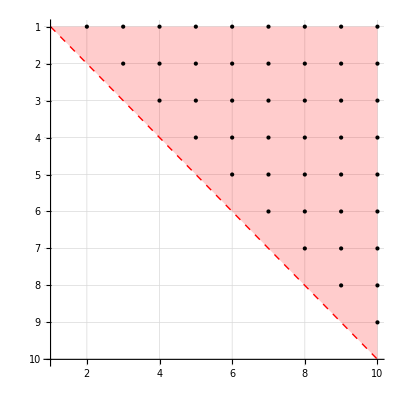

```mathematica
(* Plot adjacency matrix *)
P=DGRandomMDGP[10];
DGPlotAdjacencyMatrix[P["G"],True]
```

## 2) Check Solution and Standard Solvers

Solution Analysis
DGRelativeResidue, DGLDME, DGRMSD

## Source Code

```mathematica
ClearAll[DGRelativeResidue,DGRMSD,DGLDME]
DGRelativeResidue[G_,X_,verbose_:False]:=Module[
{i,j,k,lij,uij, dij,numberOfEdges,E,error},
E=EdgeList[P["G"]];
numberOfEdges=Length[E];
error=Table[0,{i,numberOfEdges}];
For[k=1,k≤numberOfEdges,k++,
{i=E[[k]][[1]],j=E[[k]][[2]]};
{lij,uij}=DGEdgeDistanceBounds[G,i<->j];
dij=Norm[X[[i]]-X[[j]]];
error[[k]]=Max[Max[{0,lij-dij}]/lij,Max[{0,dij-uij}]/uij];
];
If[verbose,
Print["Solution Quality"];
Print["Number of nodes      : ",Length[X]];
Print["Number of edges      : ",Length[E]];
Print["Relative error bounds: ",{Min[error],Max[error]}];
Print["Mean relative error  : ",Mean[error]]];
Return[error]
];

DGRelativeResidue[G_,X_,nodes_,i_]:=
(* Calculates the relative residue of the nodes[[i]] considering only the nodes[[1;;i-1]] *)
Module[
(* local variables *)
{eij,j,k,V,Xi,Xj,Dij,Lij,Uij,errorDij,nid},
(* current position *)
Xi=X[[nodes[[i]]]];
(* indentifies which nodes has been already fixed *)
nid=Table[0,{k,i}];
For[k=1,k≤i,k++,
nid[[nodes[[k]]]]=k
];
(* considering only the precedent nodes *)
V= Select[AdjacencyList[G,nodes[[i]]],MemberQ[nid,#]&];
(*Print["V=",V];*)
errorDij=0.0;
For[k=1,k≤Length[V],k++,
(* neighbor index *)
j=V[[k]];
(* neighbor coordinate *)
Xj=X[[j]];
(* actual distance *)
Dij=EuclideanDistance[Xi,Xj];
(* distance bounds *)
{Lij,Uij}=DGEdgeDistanceBounds[G,i<->j];
(* error Dij *)
eij=Max[(Lij-Dij)/Lij,(Dij-Uij)/Uij];
(* update error *)
If[eij>errorDij,errorDij=eij];
];
Return[errorDij]
];

DGLDME[G_,X_]:=Module[
{i,j,k,E,ldme=0,lij,uij,dij},
E=EdgeList[G];
For[k=1,k≤Length[E],k++,
{lij,uij}=DGEdgeDistanceBounds[G,E[[k]]];
i=E[[k]][[1]];
j=E[[k]][[2]];
dij=Norm[X[[i]]-X[[j]],2];
ldme+=Max[lij-dij,dij-uij,0]^2
];
Return[Sqrt[ldme/Length[E]]]
];

DGRMSD[X_,Y_]:=Module[
{xc,yc,x,y,U,D,V,rmsd},
(* calculating centers *)
xc=Mean[X];
yc=Mean[Y];
(* translation *)
x=Table[X[[i]]-xc,{i,Length[X]}];
y=Table[Y[[i]]-yc,{i,Length[Y]}];
(* svd *)
V=Transpose[x].y;
{U,D,V}=SingularValueDecomposition[V];
V=U.Transpose[V];
x=x.V;
rmsd=Norm[x-y,"Frobenius"]/Sqrt[Length[x]];
Return[{rmsd,V,x,y}]
]
```

## Examples

```mathematica
(* DGRMSD *)
X={{0.814700,0.097500,0.157600},{0.905800,0.278500,0.970600},{0.127000,0.546900,0.957200},{0.913400,0.957500,0.485400},{0.632400,0.964900,0.800300}};
Y={{6.167723,5.509229,5.376972},{5.921716,5.625914,6.161379},{5.265461,5.705450,6.339958},{5.936486,6.432611,5.883000},{5.680966,5.982123,5.893736}};
{MatrixForm[X],MatrixForm[Y]}
{rmsd,Q,x,y}=DGRMSD[X,Y];
{rmsd,MatrixForm[Q],MatrixForm[x],MatrixForm[y]}
```

```mathematica
(* Check relative error *)
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
DGRelativeResidue[P["G"],x,True]
DGRelativeResidue[P["G"],x+RandomReal[0.1,Length[x]],True]
```

```mathematica
x = {{0, 0, 0}, {1, 0, 0}, {0, 1, 0}, {1, 1, 1}, {0, 1, 1}};
P = DGProblem[x];
x[[4]]+=0.1;
DGRelativeResidue[P["G"],x,{1,2,3,4,5},4]
```

General Methods
DGNSolve, DGAllInstancesSolver, DGOptSolver

## DGNSolve - Nonlinear equations

### Source Code

```mathematica
ClearAll[DGNSolve]
DGNSolve[G_]:=Module[{k,i,j,d,d12,eqs,xi,xj,x,n},
{i,j,d}=DGGraphGetIJD[G];
eqs=Table[0,{k,Length[i]}];
n=Max[i,j];
x=Table[Symbol[StringJoin["x",ToString[xi],ToString[xj]]],{xi,n},{xj,3}];
For[k=1,k≤Length[i],k++,
xi=x[[i[[k]]]];
xj=x[[j[[k]]]];
eqs[[k]]=(xi[[1]]-xj[[1]])^2+(xi[[2]]-xj[[2]])^2+(xi[[3]]-xj[[3]])^2==d[[k]]^2
];
(* set some points *)
d12=DGEdgeWeight[G,1<->2];
eqs=Join[eqs,
{x[[1]][[1]]==0,x[[1]][[2]]==0,x[[1]][[3]]==0,
x[[2]][[1]]==d12,x[[2]][[2]]==0,x[[2]][[3]]==0}
];
Print["eqs=",TableForm[eqs]];
x=Flatten[x];
Quiet[x=NSolve[eqs,x,Reals]];
x=ArrayReshape[x,{n,3}];
Print["x=",TableForm[x]];
(* convert relations to scalar matrix *)
If[Length[x[[1]][[1]]]>1,x=Table[x[[i]][[j]][[2]],{i,n},{j,3}]];
Return[x]
];
```

### Examples

#### Example: 5 points and 4 constraints

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
eij={{1,2},{1,3},{2,3},{2,5}};
P=DGProblem[x,eij];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
TableForm[x,TableHeadings->{Table[i,{i,Length[x]}],{"x","y","z"}}]
DGRelativeResidue[P["G"],x,True];
```

#### Example: 5 points and 4 constraints (failed)

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
eij={{1,2},{1,3},{2,3},{2,5}};
P=DGProblem[x,eij];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

#### Example: 5 points and all constraints

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
P=DGProblem[x];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
TableForm[x,TableHeadings->{Table[i,{i,Length[x]}],{"x","y","z"}}]
DGRelativeResidue[P["G"],x,True];
```

#### Example: 5 points and all constraints (failed)

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
P=DGProblem[x];
DGPrintGraph[P["G"]];
x=DGNSolve[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

## DGOptSolver - Optimization

### Source Code

```mathematica
ClearAll[DGOptSolverFobj,DGOptSolver]
```

```mathematica
DGOptSolverFobj[i_,j_,d_,x_]:=Module[{f=0,numberOfAtoms,ncols,nrows,k,y},
y=ArrayReshape[x,{Length[x]/3,3}];
For[k=1,k≤Length[d],k++,
f+=(d[[k]]^2-Norm[y[[i[[k]]]]-y[[j[[k]]]]]^2)^2
];
Return[f]
]
DGOptSolver[G_]:=Module[{numberOfAtoms,f,y,v,w,i,j,d},
{i,j,d}=DGGraphGetIJD[G];
numberOfAtoms=Max[{i,j}];
ClearAll[z];
y=Array[z,3*numberOfAtoms];
f:=DGOptSolverFobj[i,j,d,#]&;
{v,y}=NMinimize[f[y],y];
y=ArrayReshape[y,{Length[y]/3,3}];
y=Table[y[[iloc]][[jloc]][[2]],{iloc,Length[y]},{jloc,3}];
Return[y]
]
```

### Examples

```mathematica
(* Example C: Solving an instance with 5 points using optimization based method *)
x=RandomReal[1,{5,3}];
eij={{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{4,5}};
P=DGProblem[x,eij];
y=DGOptSolver[P["G"]];
DGRelativeResidue[P["G"],y,True];
```

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
eij={{1,2},{1,3},{2,3},{2,5}};
P=DGProblem[x,eij];
DGPrintGraph[P["G"]];
x=DGOptSolver[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

```mathematica
(* Example D: Solving an instance with 100 points using optimization based method *)
(* It can take a lot of time!!! *) 
(* For[k=1,k≤100,k++,
SeedRandom[k];
x=RandomReal[1,{7,3}];
eij=MDGAllPairs[Length[x]];
eij=RandomSample[eij,Round[0.50Length[eij]]];
{i,j,d}=MDGCreateInstanceFromSolutionAndPairs[x,eij];
y=MDGOptSolver[i,j,d];
f=CheckMDGSolution[i,j,d,y,False];
If[Or[f>0.01,Mod[k,10]==0],
Print["{Seed,Error}=",{k,f}];
];
]
*)
```

## DGAllIstancesSolver - Solver for complete distance matrices

### Source Code

```mathematica
ClearAll[DGAllInstancesSolver]
DGAllInstancesSolver[G_]:=Module[{numberOfAtoms,k,m,λ,v,x,i,j,d},
{i,j,d}=DGGraphGetIJD[G];
numberOfAtoms=Max[{i,j}];
(* creates distance matrix *)
m=Table[0,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
For[k=1,k≤Length[i],k++,
m[[i[[k]]]][[j[[k]]]]=d[[k]];
m[[j[[k]]]][[i[[k]]]]=d[[k]];
];
(* λ:eigenvalues and v:eigenvectors *)
m=Table[(m[[1]][[iloc]]^2+m[[1]][[jloc]]^2-m[[iloc]][[jloc]]^2)/2,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
{λ,v}=Eigensystem[m,3];
(* getting solution *)
x=Table[Sqrt[λ[[jloc]]]v[[jloc]][[iloc]],{iloc,numberOfAtoms},{jloc,3}];
Return[x]
]
```

### Examples

#### Example: 5 points and 4 constraints where DGNSolve fails

```mathematica
x={
{0.732761,0.169653,0.656641},
{0.246863,0.660452,0.742898},
{0.426759,0.729058,0.897434},
{0.100975,0.670080,0.241258},
{0.204643,0.236955,0.655968}
};
P=DGProblem[x];
DGPrintGraph[P["G"]];
x=DGAllInstancesSolver[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

#### Example: 100 points all constraints

```mathematica
x=RandomReal[1,{100,3}];
P=DGProblem[x];
x=DGAllInstancesSolver[P["G"]];
DGRelativeResidue[P["G"],x,True];
```

## 3) Ordering, BuildUP, BP and IBP

Ordering
DGOrdering, DGNaturalOrdering

### Source Code

```mathematica
ClearAll[DGOrdering,DGNaturalOrdering]
DGOrdering[G_,C_,verbose_:False]:=
(* Finds an order such that all atoms could be determined by following it; 
   C: Initial clique used to start the ordering;
   G: Instance graph;
*)
Module[{i,j,k,neighs,nAtoms,nFixedAtoms,nFixedNeighs,atomsToBeFixed,atomOrder, order,minNeighsToBeFixed},
(* initial values *)
minNeighsToBeFixed=Length[C];
nAtoms=Length[VertexList[G]];
nFixedNeighs=Table[0,{i,nAtoms}];
atomOrder=Table[0,{i,nAtoms}];
atomsToBeFixed=C;
nFixedNeighs[[C]]=Infinity;
nFixedAtoms=0;
While[Length[atomsToBeFixed]>0,
If[verbose,
Print["nFixedNeighs=",nFixedNeighs];
Print["atomsToBeFixed=",atomsToBeFixed];
];
i=First[atomsToBeFixed];
(* remove the first element *)
atomsToBeFixed=Rest[atomsToBeFixed];
(* skipped: already fixed *)
If[atomOrder[[i]]>0,Continue[]];
If[verbose,Print["Fixing: ",i]];
atomOrder[[i]]=++nFixedAtoms;
If[verbose,Print["atomOrder=",atomOrder]];
(* update neighs score *)
neighs=AdjacencyList[G,i];
If[verbose,Print["neighs=",neighs]];
For[k=1,k≤Length[neighs],k++,
j=neighs[[k]];
nFixedNeighs[[j]]++;
If[atomOrder[[j]]==0&&nFixedNeighs[[j]]≥minNeighsToBeFixed &&Not[MemberQ[atomsToBeFixed,j]],
AppendTo[atomsToBeFixed,j];
];
]
];
If[nFixedAtoms≠nAtoms,Throw["InvalidOrdering: It has not been possible the set ordering."]];
order=Table[i,{i,nAtoms}];
order[[atomOrder]]=order;
Return[order];
]

DGNaturalOrdering[G_]:=Array[#&,Length[VertexList[G]]];
```

### Examples

#### Simple Example: The initial ordering is ok!

```mathematica
G=Graph[{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}];
{GraphPlot[G,VertexLabeling->True],DGPlotAdjacencyMatrix[G,True]}
i=DGOrdering[G,{1,2,3,4},True]
```

#### Harder Example: The initial ordering is not valid

```mathematica
edges={1<->2,1<->3,1<->4,1<->7,1<->8,2<->3,2<->4,2<->5,2<->6,2<->8,3<->4,3<->7,3<->8,4<->6,4<->7,4<->8,4<->5,5<->6,5<->7,6<->7,6<->8,7<->8};
G=Graph[edges];
{GraphPlot[G,VertexLabeling->True],DGPlotAdjacencyMatrix[G,True]}
i=DGOrdering[G,{1,2,3,4},True]
```

Intersection of spheres
DGIntersect3Spheres, DGIntersect4Spheres

```mathematica
ClearAll[DGIntersect3Spheres,DGIntersect4Spheres];
DGIntersect3Spheres[a_,ra_,b_,rb_,c_,rc_]:=
(* Gets the 2 solutions of {||x-a||=ra,||x-b||=rb,||x-c||=rc};
   Input;
   a,b,c: sphere centers;
   ra,rb,rc: respective sphere radius;
   Output;   
   x: the two intersections (x[[1]]: positive chirality and x[[2]]: negative chirality);
 *)
Module[{n,A,x,p,dp,u,v,w,du,dv,dw,dpu,AbsCos,error},
(* select the most perpendicular vertex angle (stability) *)
AbsCos[u_,v_]:=Dot[u,v]/(Norm[u]*Norm[v]);
{u,v,w,du,dv,dw}=MinimalBy[{
{AbsCos[b-a,c-a],{a,b,c,ra,rb,rc}},
{AbsCos[c-b,a-b],{b,c,a,rb,rc,ra}},
{AbsCos[a-c,b-c],{c,a,b,rc,ra,rb}}
},First][[1]][[2]];
(* normal to the plane (u,v,w) *)
n=Normalize[Cross[v-u,w-u]];
A={v-u,w-u,n};
x={(Dot[v,v]-Dot[u,u]-dv^2+du^2)/2,(Dot[w,w]-Dot[u,u]-dw^2+du^2)/2,Dot[n,u]};
p=LinearSolve[A,x];
(* select the factor with minimal canceling effect (stability) *)
{u,du}=MaximalBy[{
{Abs[(ra-Norm[p-a])/ra],{a,ra}},
{Abs[(rb-Norm[p-b])/rb],{b,rb}},
{Abs[(rc-Norm[p-c])/rc],{c,rc}}
},First][[1]][[2]];
dpu=Norm[p-u];
dp=N[Sqrt[(du+dpu)*(du-dpu)]];
(*dp=Re[dp]*);
x={p+dp*n,p-dp*n};
(*Print["a=",a,"  ra=",ra,"  b=",b,"  rb=",rb,"  c=",c,"  rc=",rc];
Print["p=",p,"  dp=",dp,"  x=",x];*)
(* calculating max relative errors of each solution *)
error=Table[Max[Abs[{(Norm[a-x[[i]]]-ra)/ra,(Norm[b-x[[i]]]-rb)/rb,(Norm[c-x[[i]]]-rc)/rc}]],{i,2}];
Return[{x,error}];
];

DGIntersect4Spheres[a_,ra_,b_,rb_,c_,rc_,d_,rd_]:=
Module[{x,error,errd1,errd2},
{x,error}=DGIntersect3Spheres[a,ra,b,rb,c,rc];
errd1=Abs[N[Norm[x[[1]]-d]]-rd];
errd2=Abs[N[Norm[x[[2]]-d]]-rd];
If[errd1<errd2,
x=x[[1]];
error=Max[error[[1]],errd1],
x=x[[2]];
error=Max[error[[2]],errd2]
];
Return[{x,error}]
];
```

DGBuildUpSolver
DGBuildUpInitX, DGBuildUpSetX, DGBuildUpSolver

### Source Code

```mathematica
ClearAll[
DGBuildUpInitX,
DGBuildUpSetX,
DGBuildUpSolver
]

DGBuildUpInitX[G_,basis_]:=Module[
{i1,i2,i3,i4,d12,d13,d14,d23,d24,d34,A,X,X21,X31,X32,X41,X42,error},
{i1,i2,i3,i4}=basis;
{d12,d13,d14,d23,d24,d34}=DGEdgeWeight[G,{i1<->i2,i1<->i3,i1<->i4,i2<->i3,i2<->i4,i3<->i4}];
(* set the position of the four atoms in the basis *)
X=Table[{0,0,0},{i,Length[VertexList[G]]}];
X[[i2]][[1]]=d12;
X21=X[[i2]][[1]];
X[[i3]][[1]]=(d13^2-d23^2+X21^2)/(2*X21);
X31=X[[i3]][[1]];
X[[i3]][[2]]=Sqrt[d13^2-X31^2];
{X[[i4]],error}=DGIntersect3Spheres[X[[i1]],d14,X[[i2]],d24,X[[i3]],d34][[1]];
Return[X];
];

DGBuildUpSetX[G_,X_,nodes_,i_]:=Module[
{j,k,neighs,basis,x,i1,i2,i3,i4,d1,d2,d3,d4,error},
k=nodes[[i]];
neighs=Intersection[AdjacencyList[G,k],nodes[[1;;(i-1)]]];
If[Length[neighs]<4,Throw["InvalidOrder: There is not enough neighs to set a basis"]];
basis=Subsets[neighs,{4}];
For[j=1,j≤Length[basis],j++,
{i1,i2,i3,i4}=basis[[j]];
{d1,d2,d3,d4}=DGEdgeWeight[G,{i1<->k,i2<->k,i3<->k,i4<->k}];
{x,error}=DGIntersect4Spheres[X[[i1]],d1,X[[i2]],d2,X[[i3]],d3,X[[i4]],d4];
If[error<10^(-3),Break];
];
If[error>10^(-3),Throw["InvalidSolution: A precise solution could not be found."]];
Return[x]
];

DGBuildUpSolver[G_,nodes_]:=Module[
{i,X},
X=DGBuildUpInitX[G,nodes[[1;;4]]];
(* set remaining atoms *)
For[i=5,i≤Length[X],i++,
X[[nodes[[i]]]]=DGBuildUpSetX[G,X,nodes,i]
];
Return[X]
];
```

### Example

#### Check DGBuildUpInitX

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
edges={{1,2},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}};
P=DGProblem[x,edges];
DGPrintGraph[P["G"]]
basis={2,3,4,5};
x=DGBuildUpInitX[P["G"],basis];
DGPrintDistanceMatrix[x,edges]
```

#### Check DGBuildUpSolver

```mathematica
x={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0}};
edges={{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5}};
P=DGProblem[x,edges];
nodes={1,2,3,5,4};
x=DGBuildUpSolver[P["G"],nodes];
DGPrintX[x]
DGRelativeResidue[P["G"],x,True];
```

#### Solving an instance using BuilUpSolver method

```mathematica
P=DGRandomMDGP[20,0.0,5.0,0];
X=P["X"];
G=P["G"];
nodes=Table[i,{i,Length[VertexList[G]]}]
X=DGBuildUpSolver[G,nodes];
DGRelativeResidue[G,X,True];
```

DGBPSolver

## Source Code

```mathematica
ClearAll[DGBPXinit,DGBPGetX,DGBPSolver]
DGBPXinit[G_,basis_]:=Module[{a,b,c,numberOfAtoms,dab,dac,dbc,θ,X},
numberOfAtoms=Length[VertexList[G]];
X=Table[{0,0,0},{i,numberOfAtoms}];
(* three first atoms *)
{a,b,c}=basis[[1;;3]];
{dab,dac,dbc}=DGEdgeWeight[G,{a<->b,a<->c,b<->c}];
(* planar rotation angle for third atom *)
θ=ArcCos[(dab^2+dbc^2-dac^2)/(2*dab*dbc)];
(* set the position of the three first points *)
X[[{a,b,c}]]={{0,0,0},{-dab,0,0},{-dab+dbc*Cos[θ],dbc*Sin[θ] ,0}};
Return[X];
]

DGBPGetX[G_,X_,branch_,nodes_,i_]:=Module[
{j,k,neighs,x,error,i1,i2,i3,d1,d2,d3},
k=nodes[[i]];
neighs=Intersection[AdjacencyList[G,k],nodes[[1;;(i-1)]]];
If[Length[neighs]<3,Throw["InvalidOrder: There is not enough neighs to set a basis"]];
(*Print["neighs=",neighs," k=",k];*)
{i1,i2,i3}=neighs[[1;;3]];
{d1,d2,d3}=DGEdgeWeight[G,{i1<->k,i2<->k,i3<->k}];
{x,error}=DGIntersect3Spheres[X[[i1]],d1,X[[i2]],d2,X[[i3]],d3];
Return[x[[branch+1]]]
];

DGBPSolver[G_,nodes_,onesol_:False,verbose_:False]:=
(* Calculate all solutions of the DMDGP instance defined by the graph G. *)
Module[
(* local variables *)
{i,k,numberOfAtoms,prune,branch,X,S,work,error,tol=10^(-5)},
numberOfAtoms=Length[VertexList[G]];
X=DGBPXinit[G,nodes[[1;;3]]];
(* init BPTree *)
branch=Table[0,{i,numberOfAtoms}];branch[[1;;3]]=1;
work=Table[0,{i,numberOfAtoms}];work[[1;;3]]=1;
(* solutions and branches *)
S=<|"Points"->{},"Branches"->{}|>;
k=4;
While[k>3,
work[[k]]++;
X[[nodes[[k]]]]=DGBPGetX[G,X,branch[[k]],nodes,k];
error=DGRelativeResidue[G,X,nodes,k];
prune=error>tol;
(*Print["[bp] k=",k,"  branch=",branch,"  error=",NumberForm[error,{3,2}],"  prune=",prune];*)
(*DGPrintX[X[[nodes[[1;;k]]]]];*)
(* solution found *)
If[Not[prune]&&k==numberOfAtoms ,
AppendTo[S["Points"],X];
AppendTo[S["Branches"],branch];
If[onesol,Return[{S,work}]];
];
(* update tree node *)
prune=prune||k==Length[branch];
If[prune&&branch[[k]]==1,
While[k>3&&branch[[k]]==1,k--];
];
If[prune&&branch[[k]]==0,
branch[[k]]=1;
For[i=k+1,i≤Length[branch],i++,branch[[i]]=0];
];
If[Not[prune],k++];
];
If[verbose,
Print["DGBPSolver"];
Print["Number of solutions: ",Length[S["Points"]]]
];
Return[{S,work}]
];
```

## Examples and Applications

### Easy case using natural order

```mathematica
P=DGRandomMDGP[20,0.0,5];
nodes=DGNaturalOrdering[P["G"]];
{S,work}=DGBPSolver[P["G"],nodes,False,True];
DGRelativeResidue[P["G"],S["Points"][[1]],True];
```

### Instance with more than two solutions

```mathematica
x=RandomReal[1,{6,3}];
edges=DGEdgesMDGP[Length[x]];
AppendTo[edges,{1,6}]
P=DGProblem[x,edges];
nodes=DGNaturalOrdering[P["G"]];
{S,work}=DGBPSolver[P["G"],nodes,False,True];
```

### Calculating the number of solution as a function of the number of constraints (max distance)

```mathematica
G=DGRandomMDGP[10]["G"]
nSample=25;
density={0,0.1,0.2,0.3,0.4,0.5}; (* density of edges *)
(* generating sample data *)
Needs["ErrorBarPlots`"]
allEdges=EdgeList[G]
nSols=Table[0,{i,Length[density]},{j,nSample}];
g=Table[0,{i,Length[density]},{j,nSample}];
For[i=1,i≤Length[density],i++,
d=density[[i]];
For[j=1,j≤nSample,j++,
(* create subgraph *)
gij=G;
For[k=1,k≤Length[allEdges],k++,
ek=allEdges[[k]];
If[RandomReal[]>d&&Abs[ek[[1]]-ek[[2]]]>3,gij=EdgeDelete[gij,ek]]
];
g[[i]][[j]]=gij;
(* solve instance *)
nodes=Table[i,{i,Length[VertexList[gij]]}];
{S,work}=DGBPSolver[gij,nodes];
nSols[[i]][[j]]=Length[S["Points"]];
];
];
(* plot results *)
ErrorListPlot[Table[{{density[[i]],Mean[nSols[[i]]]},ErrorBar[StandardDeviation[nSols[[i]]]]},{i,Length[density]}],
Joined->True,
AxesLabel->{"Density of Edges", "Number of Solutions"}]
```

IBPSolver

## Source Code

```mathematica
ClearAll[DGIPBSubG,DGIBPSolver];

DGIPBSubG[G_,k_,branch_,nslices_]:=Module[{i,E,W=G,nodes,ei,ej,dij,lij,uij},
(* Delete vertices k+1,...,numberOfAtoms *)
nodes=Table[i,{i,k+1,Length[VertexList[G]]}];
W=VertexDelete[G,nodes];
E=EdgeList[W];
dij=Table[0,{i,Length[E]}];
lij=Table[0,{i,Length[E]}];
uij=Table[0,{i,Length[E]}];
For[i=1,i≤Length[E],i++,
{lij[[i]],uij[[i]]}=DGEdgeDistanceBounds[G,E[[i]]];
dij[[i]]=DGEdgeWeight[G,E[[i]]];
(* set weight affected by branch *)
ei=E[[i]][[1]];
ej=E[[i]][[2]];
If[ei>ej,{ei,ej}={ej,ei}];
If[ej-ei==3,
dij[[i]]=(uij[[i]]-lij[[i]])/nslices;
dij[[i]]=dij[[i]]*branch[[ej]]+lij[[i]]+dij[[i]]/2.0;
];
];
W=Graph[E,EdgeWeight->dij];
For[i=1,i≤Length[E],i++,
PropertyValue[{W,E[[i]]}, "DistanceBounds"] = {lij[[i]],uij[[i]]};
];
Return[W];
];

DGIBPSolver[G_,nslices_,verbose_:False]:=
(* Calculate all solutions of the DMDGP instance defined by the graph G using natural ordering. *)
Module[
(* local variables *)
{i,k,numberOfAtoms,prune,branch,W,S,SW,work,locwork,tol=10^(-5)},
numberOfAtoms=Length[VertexList[G]];
(* init IBPTree *)
branch=Table[0,{i,numberOfAtoms}];branch[[1;;3]]=nslices-1;
work=Table[0,{i,numberOfAtoms}];work[[1;;3]]=1;
(* solutions and branches *)
S=<|"Points"->{},"Branches"->{}|>;
k=4;
While[k>3,
W=DGIPBSubG[G,k,branch,nslices];
{SW,locwork}=DGBPSolver[W,DGNaturalOrdering[W],k≠numberOfAtoms];
For[i=4,i≤k,i++,work[[i]]+=locwork[[i]]];
prune=Length[SW["Points"]]==0; (* unfeasible subgraph *)
(*Print["[ibp] k=",k,"  branch=",branch, "   work=",work," prune=",prune];*)
(* solution found *)
If[Not[prune]&&k==numberOfAtoms ,
S["Points"]=Join[S["Points"],SW["Points"]];
AppendTo[S["Branches"],branch]];
(* update tree node *)
prune=prune||k==Length[branch];
If[prune&&branch[[k]]==nslices-1,
While[k>3&&branch[[k]]==nslices-1,k--];
];
If[prune&&branch[[k]]<nslices-1,
branch[[k]]++;
For[i=k+1,i≤Length[branch],i++,branch[[i]]=0];
];
If[Not[prune],k++];
];
If[verbose,
Print["DGIBPSolver"];
Print["Number of solutions: ",Length[S["Points"]]]
];
Return[{S,work}]
];
```

## Examples and Applications

### Check DGIBPSubG

```mathematica
P=DGRandomMDGP[5,0.1,5.0];
branch={1,1,1,1,0};
nslices=2;
W=DGIPBSubG[P["G"],4,branch,nslices];
DGPrintGraph[P["G"]];
DGPrintGraph[W];
```

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 2.8679 | 2.58111 | 3.15469
4 | 1 | 5 | 3.18887 | 2.86998 | 3.50776
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 2.78798 | 2.50918 | 3.06677
8 | 3 | 4 | 1.526 | 1.526 | 1.526
9 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
10 | 4 | 5 | 1.526 | 1.526 | 1.526

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.01129 | 2.58111 | 3.15469
4 | 2 | 3 | 1.526 | 1.526 | 1.526
5 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
6 | 3 | 4 | 1.526 | 1.526 | 1.526

### Solving a small instance using DGIBP

```mathematica
P=DGRandomMDGP[5,0.1,5.0];
{S,work}=DGIBPSolver[P["G"],2,True];
```

DGIBPSolver

Number of solutions: 0

### Illustrating the tree exponential growth

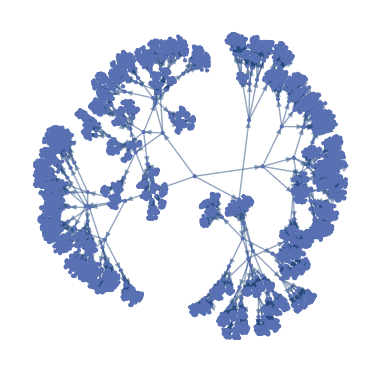

Number of Vertex=5461

```mathematica
(* Plot IBP Tree (it can be very slow!!!) *)
numberOfAtoms=9;
numberOfSlices=2; (* or 2 at max *)
node=3;
edges={};
count=3;
For[i=1,i≤2*numberOfSlices,i++,
AppendTo[edges,node->(++count)]
];
T=TreeGraph[edges];
For[k=5,k≤numberOfAtoms,k++,
leafs=Select[VertexList[T],VertexDegree[T,#]===1&];
count=Max[VertexList[T]];
For[i=1,i≤Length[leafs],i++,
node=leafs[[i]];
For[j=1,j≤2*numberOfSlices,j++,
AppendTo[edges,node->(++count)]
]
];
T=TreeGraph[edges];
]
Print[T]
Print["Number of Vertex=",Length[VertexList[T]]]
```

```mathematica
(* Number of nodes on IBP tree *)
NumberOfIBPVertex[numberOfAtoms_,numberOfSlices_]:=Module[{},((2*numberOfSlices)^(numberOfAtoms-2)-1)/((2*numberOfSlices)-1)];
NumberOfIBPVertex[9,1]
```

```mathematica
xy=Table[{i,NumberOfIBPVertex[9,i]},{i,10}];
ListLogPlot[xy,Joined->True,PlotLabel->"Number of Vertex on IBP Tree"]
```

```mathematica
(* Top 1: Sunway TaihuLight at 93 petaflops (10^15 flops) on November 2016 *)
xy=Table[{i,NumberOfIBPVertex[i,4]/(365*24*3600*(93*10^15))},{i,40}];
ListLogPlot[xy,Joined->True,PlotLabel->"Time to compute IBP tree on 93 petaflops",AxesLabel->{"Number of Atoms","Years"}]
```

## 4) Solving Manually

Solving Manually: Continuos Problem

## Applet

```mathematica
ClearAll[DGByHandGetX,DGByHandErrorMatrix];
DGByHandGetX[θ_]:=Module[{n,d=1.526,ϕ=1.91,a,b,c,i,p,u,v,x},
n=Length[θ];
x=Table[0,{i,n},{j,3}];
x[[{1,2,3}]]={{0,0,0},{-d,0,0},{-d+d*Cos[ϕ],d*Sin[ϕ] ,0}};
For[i=4,i≤n,i++,
(* dihedral rotation axis *)
{a,b,c}={x[[i-3]],x[[i-2]],x[[i-1]]};
u=Normalize[b-c];
p= c+d* u; 
(* normal to the plane abc *)
v=Cross[b-c,a-c];
(* plane rotation *)
p=RotationTransform[ϕ,v,c][p];
(* dihedral rotation *)
p=RotationTransform[θ[[i]],u,c][p];
(* set i-th coordinate *)
x[[i]]=p
];
Return[x]
];

DGByHandErrorMatrix[G_,x_]:=Module[{i,j,k,edges,M,dij},
M=Table[0,{i,Length[x]},{j,Length[x]}];
edges=EdgeList[G];
For[k=1,k≤Length[edges],k++,
i=edges[[k]][[1]];
j=edges[[k]][[2]];
dij=DGEdgeWeight[G,i<->j];
M[[i]][[j]]=Abs[(Norm[x[[i]]-x[[j]]]-dij)/dij];
M[[j]][[i]]=M[[i]][[j]];
];
Return[M]
];

ω=RandomReal[{-Pi,Pi},9]
x=DGByHandGetX[ω];
G=DGProblem[x]["G"];
DynamicModule[{},
Manipulate[{
Graphics3D[{
{Red,Tube[DGByHandGetX[{0,0,0,ω4,ω5,ω6,ω7,ω8,ω9}]]},
{PointSize[Large],Blue,Point[DGByHandGetX[{0,0,0,ω4,ω5,ω6,ω7,ω8,ω9}]]}},
PlotRange->{xrange,yrange,zrange},
RotationAction->"Clip",
Axes->True,
AxesLabel->{"x","y","z"},
PlotLabel->{"Mean(error):",NumberForm[Max[DGByHandErrorMatrix[G,DGByHandGetX[{0,0,0,ω4,ω5,ω6,ω7,ω8,ω9}]]],{3,2}]},
BoxStyle->Directive[Dashed],
ImageSize->Medium],
MatrixPlot[DGByHandErrorMatrix[G,DGByHandGetX[{0,0,0,ω4,ω5,ω6,ω7,ω8,ω9}]],ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False]},
(* Torsion angles *)
Style["Torsion Angles",Bold,Medium],
{{ω4,0},-Pi,Pi},
{{ω5,0},-Pi,Pi},
{{ω6,0},-Pi,Pi},
{{ω7,0},-Pi,Pi},
{{ω8,0},-Pi,Pi},
{{ω9,0},-Pi,Pi},
(* Bounding boxes *)
Style["Bounding Limits",Bold,Medium],
{{xrange,{-3,3}},-10,10,ControlType -> IntervalSlider,Method -> "Push",MinIntervalSize->0.1},
{{yrange,{-3,3}},-10,10,ControlType -> IntervalSlider,Method -> "Push",MinIntervalSize->0.1},
{{zrange,{-3,3}},-10,10,ControlType -> IntervalSlider,Method -> "Push",MinIntervalSize->0.1},
OpenerView[
{Style["Solution",Bold, Medium],
Column[
{Row[{"ω4  ",Slider[ω[[4]],{-Pi,Pi},Enabled->False]}],
Row[{"ω5  ",Slider[ω[[5]],{-Pi,Pi},Enabled->False]}],
Row[{"ω6  ",Slider[ω[[6]],{-Pi,Pi},Enabled->False]}],
Row[{"ω7  ",Slider[ω[[7]],{-Pi,Pi},Enabled->False]}],
Row[{"ω8  ",Slider[ω[[8]],{-Pi,Pi},Enabled->False]}],
Row[{"ω9  ",Slider[ω[[9]],{-Pi,Pi},Enabled->False]}]}]}],
ControlPlacement->Left]
]
```

Solving Manually: Discrete Problem

## Applet

```mathematica
ClearAll[DGByHandTreeFromBranches]
DGByHandTreeFromBranches[G_,branch_,branches_,check_]:=Module[
{T,X,k,i,n,b,x,y,z,dx,dy,dz,edges={},v={},styVertex,styEdges={},m,color,valid,nodes},
nodes=DGNaturalOrdering[G];
n=Length[VertexList[G]]-3;
(* creating edges *)
For[k=1,k≤2^n-1,k++,
AppendTo[edges,k<->2k];
AppendTo[edges,k<->2k+1];
];
(* highlighting current branch *)
For[k=0,k≤n,k++,
AppendTo[v,FromDigits[Join[{1},branch[[1;;k]]],2]];
If[k>0,
AppendTo[styEdges,v[[k]]<->v[[k+1]]->{Blue,Thickness[0.01]}]
];
];
(* coloring visited nodes (branches) *)
styVertex={LightGray};
If[Length[branches]>0,
For[k=1,k≤Length[branches],k++,
X=DGBPXinit[G,nodes[[1;;3]]];
b=branches[[k]];
If[check,
(* checking partial solutions *)
valid=True;
For[i=1,i≤n,i++,
X[[i+3]]=DGBPGetX[G,X,b[[i]],nodes,i+3];
If[valid&&DGRelativeResidue[G,X,nodes,i+3]<0.001,
color=Green,
valid =False;
color=Red;
];
v=FromDigits[Join[{1},b[[1;;i]]],2];
AppendTo[styVertex,v->color]
],
(* checking only final solution *)
valid=True;
For[i=1,i≤n,i++,
X[[i+3]]=DGBPGetX[G,X,b[[i]],nodes,i+3];
If[DGRelativeResidue[G,X,nodes,i+3]>0.001,
valid=False
];
If[valid,color=Green,color=Red];
v=FromDigits[Join[{1},b],2];
AppendTo[styVertex,v->color]
],
];
];
];
T=TreeGraph[
edges,
VertexStyle->styVertex,
EdgeStyle->styEdges,
GraphLayout->{"LayeredEmbedding",LayerSizeFunction->(8&)}
];
Return[T];
];

G=DGRandomMDGP[9,0.0,5.0]["G"];
nodes=DGNaturalOrdering[G];
DynamicModule[{branches={},b={},s={},node,X=DGBPXinit[G,nodes[[1;;3]]]},
Manipulate[
Row[{DGByHandTreeFromBranches[G,{ω4,ω5,ω6,ω7,ω8,ω9},branches,BP],
Column[
{DGPlotAdjacencyMatrix[G,Sym],
Graphics3D[{
{Red,Tube[X]},
{PointSize[Large],Blue,Point[X]}}],
MatrixForm[s,TableHeadings->{None,{"ω4","ω5","ω6","ω7","ω8","ω9"}}]}]}],
(* Branches *)
Style["Branches",Bold,Medium],
{ω4,{0,1},ControlType->SetterBar},
{ω5,{0,1},ControlType->SetterBar},
{ω6,{0,1},ControlType->SetterBar},
{ω7,{0,1},ControlType->SetterBar},
{ω8,{0,1},ControlType->SetterBar},
{ω9,{0,1},ControlType->SetterBar},
Button["Try",
{b={ω4,ω5,ω6,ω7,ω8,ω9},
For[node=1,node≤Length[b],node++,
X[[node+3]]=DGBPGetX[G,X,b[[node]],nodes,node+3];
],
AppendTo[branches,{ω4,ω5,ω6,ω7,ω8,ω9}]},
Background->LightBlue],
Delimiter,
Style["Options",Bold, Medium],
{BP,{False,True},ControlType->Checkbox},
{Sym,{False,True},ControlType->Checkbox},
Delimiter,
(* show solutions *)
Style["Solutions",Bold,Medium],
Button["Show",
{s=DGBPSolver[G,nodes][[1]]["Branches"],
s=Table[s[[i]][[j]],{i,Length[s]},{j,4,9}],
branches=Union[branches,s]},
Background->LightRed
],
Button["Reset",
{G=DGRandomMDGP[9,0.0,5.0]["G"],branches={},b={},s={}},
Background->LightRed]
],
ControlPlacement->Left
]
```

## 5) Geometric Algebra

```mathematica
<<Notation`
```

## Clifford Algebra

### Basis

```mathematica
GAOneAt[n_,i_]:=Module[{v},v=Table[0,{k,n}];v[[i]]=1;Return[v]];
```

```mathematica
Notation[Subscript[e, s] ⟺ GAOneAt[32,1]]
Notation[Subscript[e, 1] ⟺ GAOneAt[32,2]]
Notation[Subscript[e, 2] ⟺ GAOneAt[32,3]]
Notation[Subscript[e, 3] ⟺ GAOneAt[32,4]]
Notation[Subscript[e, ∞] ⟺ GAOneAt[32,5]]
Notation[Subscript[e, 0] ⟺ GAOneAt[32,6]]
AddInputAlias["es"->Subscript[e, s]]
AddInputAlias["e0"->Subscript[e, 0]]
AddInputAlias["e1"->Subscript[e, 1]]
AddInputAlias["e2"->Subscript[e, 2]]
AddInputAlias["e3"->Subscript[e, 3]]
AddInputAlias["einf"->Subscript[e, ∞]]
```

```mathematica
Subscript[e, ∞]
```

{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ClearAll[GANum2Str,GAPrint]
GANum2Str[s_,x_]:=Module[{sign=""},If[StringLength[s]>0&&x>0,sign="+"];
Return[sign<>ToString[x]]];
GAPrint[x_]:=Module[{s=""},
If[Abs[x[[1]]]>0,s=s<>GANum2Str[s,x[[1]]]<>"e_r"];
If[Abs[x[[6]]]>0,s=s<>GANum2Str[s,x[[6]]]<>"e_0"];
If[Abs[x[[2]]]>0,s=s<>GANum2Str[s,x[[2]]]<>"e_1"];
If[Abs[x[[3]]]>0,s=s<>GANum2Str[s,x[[3]]]<>"e_2"];
If[Abs[x[[4]]]>0,s=s<>GANum2Str[s,x[[4]]]<>"e_3"];
If[Abs[x[[5]]]>0,s=s<>GANum2Str[s,x[[5]]]<>"e_∞"];
If[Abs[x[[7]]]>0,s=s<>GANum2Str[s,x[[7]]]<>"e_1^e_2"];
If[Abs[x[[8]]]>0,s=s<>GANum2Str[s,x[[8]]]<>"e_1^e_3"];
If[Abs[x[[9]]]>0,s=s<>GANum2Str[s,x[[9]]]<>"e_1^e_∞"];
If[Abs[x[[10]]]>0,s=s<>GANum2Str[s,x[[10]]]<>"e_1^e_0"];
If[Abs[x[[11]]]>0,s=s<>GANum2Str[s,x[[11]]]<>"e_2^e_3"];
If[Abs[x[[12]]]>0,s=s<>GANum2Str[s,x[[12]]]<>"e_2^e_∞"];
If[Abs[x[[13]]]>0,s=s<>GANum2Str[s,x[[13]]]<>"e_2^e_0"];
If[Abs[x[[14]]]>0,s=s<>GANum2Str[s,x[[14]]]<>"e_3^e_∞"];
If[Abs[x[[15]]]>0,s=s<>GANum2Str[s,x[[15]]]<>"e_3^e_0"];
If[Abs[x[[16]]]>0,s=s<>GANum2Str[s,x[[16]]]<>"e_∞^e_0"];
If[Abs[x[[17]]]>0,s=s<>GANum2Str[s,x[[17]]]<>"e_1^e_2^e_3"];
If[Abs[x[[18]]]>0,s=s<>GANum2Str[s,x[[18]]]<>"e_1^e_2^e_∞"];
If[Abs[x[[19]]]>0,s=s<>GANum2Str[s,x[[19]]]<>"e_1^e_2^e_0"];
If[Abs[x[[20]]]>0,s=s<>GANum2Str[s,x[[20]]]<>"e_1^e_3^e_∞"];
If[Abs[x[[21]]]>0,s=s<>GANum2Str[s,x[[21]]]<>"e_1^e_3^e_0"];
If[Abs[x[[22]]]>0,s=s<>GANum2Str[s,x[[22]]]<>"e_1^e_∞^e_0"];
If[Abs[x[[23]]]>0,s=s<>GANum2Str[s,x[[23]]]<>"e_2^e_3^e_∞"];
If[Abs[x[[24]]]>0,s=s<>GANum2Str[s,x[[24]]]<>"e_2^e_3^e_0"];
If[Abs[x[[25]]]>0,s=s<>GANum2Str[s,x[[25]]]<>"e_2^e_∞^e_0"];
If[Abs[x[[26]]]>0,s=s<>GANum2Str[s,x[[26]]]<>"e_3^e_∞^e_0"];
If[Abs[x[[27]]]>0,s=s<>GANum2Str[s,x[[27]]]<>"e_1^e_2^e_3^e_∞"];
If[Abs[x[[28]]]>0,s=s<>GANum2Str[s,x[[28]]]<>"e_1^e_2^e_3^e_0"];
If[Abs[x[[29]]]>0,s=s<>GANum2Str[s,x[[29]]]<>"e_1^e_2^e_∞^e_0"];
If[Abs[x[[30]]]>0,s=s<>GANum2Str[s,x[[30]]]<>"e_1^e_3^e_∞^e_0"];
If[Abs[x[[31]]]>0,s=s<>GANum2Str[s,x[[31]]]<>"e_2^e_3^e_∞^e_0"];
If[Abs[x[[32]]]>0,s=s<>GANum2Str[s,x[[32]]]<>"e_1^e_2^e_3^e_∞^e_0"];
Return[s]
];
```

### Products

#### Inner (Pq não tem z[32]? É sempre zero?)

```mathematica
GAInner[x_,y_]:=Module[{z=ConstantArray[0,32]},
z[[1]]=((((x[[9]]*y[[10]]+x[[10]]*y[[9]])-x[[8]]*y[[8]]-x[[7]]*y[[7]]-x[[5]]*y[[6]]-x[[6]]*y[[5]]-x[[32]]*y[[32]]-x[[31]]*y[[31]]+x[[4]]*y[[4]])-x[[30]]*y[[30]]-x[[29]]*y[[29]]-x[[27]]*y[[28]]-x[[28]]*y[[27]]+x[[26]]*y[[26]]+x[[25]]*y[[25]]+x[[23]]*y[[24]]+x[[24]]*y[[23]]+x[[22]]*y[[22]]+x[[20]]*y[[21]]+x[[3]]*y[[3]]+x[[21]]*y[[20]]+x[[18]]*y[[19]]+x[[19]]*y[[18]])-x[[17]]*y[[17]]+x[[16]]*y[[16]]+x[[14]]*y[[15]]+x[[15]]*y[[14]]+x[[12]]*y[[13]]+x[[13]]*y[[12]])-x[[11]]*y[[11]]+x[[2]]*y[[2]];
z[[2]]=((((x[[5]]*y[[10]]+x[[6]]*y[[9]])-x[[4]]*y[[8]]-x[[3]]*y[[7]]-x[[9]]*y[[6]]-x[[10]]*y[[5]]-x[[31]]*y[[32]]-x[[32]]*y[[31]]+x[[8]]*y[[4]])-x[[26]]*y[[30]]-x[[25]]*y[[29]]-x[[23]]*y[[28]]-x[[24]]*y[[27]]+x[[30]]*y[[26]]+x[[29]]*y[[25]]+x[[27]]*y[[24]]+x[[28]]*y[[23]]+x[[16]]*y[[22]]+x[[14]]*y[[21]]+x[[7]]*y[[3]]+x[[15]]*y[[20]]+x[[12]]*y[[19]]+x[[13]]*y[[18]])-x[[11]]*y[[17]]+x[[22]]*y[[16]]+x[[20]]*y[[15]]+x[[21]]*y[[14]]+x[[18]]*y[[13]]+x[[19]]*y[[12]])-x[[17]]*y[[11]];z[[3]]=(((((-(x[[18]]*y[[10]]))-x[[19]]*y[[9]]+x[[17]]*y[[8]]+x[[2]]*y[[7]])-x[[12]]*y[[6]]-x[[13]]*y[[5]]+x[[30]]*y[[32]])-x[[26]]*y[[31]]+x[[11]]*y[[4]]+x[[32]]*y[[30]]+x[[22]]*y[[29]]+x[[20]]*y[[28]]+x[[21]]*y[[27]]+x[[31]]*y[[26]]+x[[16]]*y[[25]]+x[[14]]*y[[24]]+x[[15]]*y[[23]])-x[[29]]*y[[22]]-x[[27]]*y[[21]]-x[[28]]*y[[20]]-x[[9]]*y[[19]]-x[[10]]*y[[18]]+x[[8]]*y[[17]]+x[[25]]*y[[16]]+x[[23]]*y[[15]]+x[[24]]*y[[14]]+x[[5]]*y[[13]]+x[[6]]*y[[12]])-x[[4]]*y[[11]]-x[[7]]*y[[2]];z[[4]]=(((((((-(x[[20]]*y[[10]]))-x[[21]]*y[[9]]+x[[2]]*y[[8]])-x[[17]]*y[[7]]-x[[14]]*y[[6]]-x[[15]]*y[[5]]-x[[29]]*y[[32]]+x[[25]]*y[[31]]+x[[22]]*y[[30]])-x[[32]]*y[[29]]-x[[18]]*y[[28]]-x[[19]]*y[[27]]+x[[16]]*y[[26]])-x[[31]]*y[[25]]-x[[12]]*y[[24]]-x[[13]]*y[[23]]-x[[30]]*y[[22]]-x[[9]]*y[[21]]-x[[11]]*y[[3]]-x[[10]]*y[[20]]+x[[27]]*y[[19]]+x[[28]]*y[[18]])-x[[7]]*y[[17]]+x[[26]]*y[[16]]+x[[5]]*y[[15]]+x[[6]]*y[[14]])-x[[23]]*y[[13]]-x[[24]]*y[[12]]+x[[3]]*y[[11]])-x[[8]]*y[[2]];z[[5]]=(((((x[[2]]-x[[22]])*y[[9]]-x[[20]]*y[[8]]-x[[18]]*y[[7]]-x[[16]]*y[[5]]+x[[27]]*y[[32]])-x[[23]]*y[[31]]-x[[14]]*y[[4]]-x[[20]]*y[[30]]-x[[18]]*y[[29]]+(x[[32]]-x[[17]])*y[[27]])-x[[14]]*y[[26]]-x[[12]]*y[[25]]+(x[[31]]-x[[11]])*y[[23]])-x[[9]]*y[[22]]-x[[12]]*y[[3]]+(x[[30]]-x[[8]])*y[[20]]+(x[[29]]-x[[7]])*y[[18]]+x[[27]]*y[[17]]+x[[5]]*y[[16]]+(x[[4]]-x[[26]])*y[[14]]+(x[[3]]-x[[25]])*y[[12]])-x[[23]]*y[[11]]-x[[9]]*y[[2]];z[[6]]=((((((x[[22]]+x[[2]])*y[[10]]-x[[21]]*y[[8]]-x[[19]]*y[[7]]+x[[16]]*y[[6]])-x[[28]]*y[[32]]+x[[24]]*y[[31]])-x[[15]]*y[[4]]+x[[21]]*y[[30]]+x[[19]]*y[[29]]+((-x[[32]])-x[[17]])*y[[28]]+x[[15]]*y[[26]]+x[[13]]*y[[25]]+((-x[[31]])-x[[11]])*y[[24]]+x[[10]]*y[[22]]+((-x[[8]])-x[[30]])*y[[21]])-x[[13]]*y[[3]]+((-x[[7]])-x[[29]])*y[[19]]+x[[28]]*y[[17]])-x[[6]]*y[[16]]+(x[[4]]+x[[26]])*y[[15]]+(x[[25]]+x[[3]])*y[[13]])-x[[24]]*y[[11]]-x[[10]]*y[[2]];z[[7]]=((-(x[[18]]*y[[6]]))-x[[19]]*y[[5]]+x[[26]]*y[[32]]+x[[17]]*y[[4]]+x[[16]]*y[[29]]+x[[14]]*y[[28]]+x[[15]]*y[[27]]+x[[32]]*y[[26]])-x[[5]]*y[[19]]-x[[6]]*y[[18]]+x[[4]]*y[[17]]+x[[29]]*y[[16]]+x[[27]]*y[[15]]+x[[28]]*y[[14]];z[[8]]=(((-(x[[20]]*y[[6]]))-x[[21]]*y[[5]]-x[[25]]*y[[32]]+x[[16]]*y[[30]])-x[[12]]*y[[28]]-x[[13]]*y[[27]]-x[[32]]*y[[25]]-x[[5]]*y[[21]]-x[[17]]*y[[3]]-x[[6]]*y[[20]]-x[[3]]*y[[17]]+x[[30]]*y[[16]])-x[[27]]*y[[13]]-x[[28]]*y[[12]];z[[9]]=(((-(x[[22]]*y[[5]]))+x[[23]]*y[[32]])-x[[20]]*y[[4]]-x[[14]]*y[[30]]-x[[12]]*y[[29]]-x[[11]]*y[[27]]+x[[32]]*y[[23]])-x[[5]]*y[[22]]-x[[18]]*y[[3]]-x[[4]]*y[[20]]-x[[3]]*y[[18]]-x[[30]]*y[[14]]-x[[29]]*y[[12]]-x[[27]]*y[[11]];z[[10]]=(((x[[22]]*y[[6]]-x[[24]]*y[[32]]-x[[21]]*y[[4]]+x[[15]]*y[[30]]+x[[13]]*y[[29]])-x[[11]]*y[[28]]-x[[32]]*y[[24]]+x[[6]]*y[[22]])-x[[4]]*y[[21]]-x[[19]]*y[[3]]-x[[3]]*y[[19]]+x[[30]]*y[[15]]+x[[29]]*y[[13]])-x[[28]]*y[[11]];z[[11]]=((x[[27]]*y[[10]]+x[[28]]*y[[9]])-x[[23]]*y[[6]]-x[[24]]*y[[5]]+x[[22]]*y[[32]]+x[[16]]*y[[31]]+x[[9]]*y[[28]]+x[[10]]*y[[27]])-x[[5]]*y[[24]]-x[[6]]*y[[23]]+x[[32]]*y[[22]]+x[[2]]*y[[17]]+x[[31]]*y[[16]]+x[[17]]*y[[2]];z[[12]]=(((x[[29]]*y[[9]]+x[[27]]*y[[8]])-x[[25]]*y[[5]]-x[[20]]*y[[32]]-x[[14]]*y[[31]]-x[[23]]*y[[4]]+x[[9]]*y[[29]]+x[[8]]*y[[27]])-x[[5]]*y[[25]]-x[[4]]*y[[23]]-x[[32]]*y[[20]]+x[[2]]*y[[18]])-x[[31]]*y[[14]]+x[[18]]*y[[2]];z[[13]]=(((-(x[[29]]*y[[10]]))+x[[28]]*y[[8]]+x[[25]]*y[[6]]+x[[21]]*y[[32]]+x[[15]]*y[[31]])-x[[24]]*y[[4]]-x[[10]]*y[[29]]+x[[8]]*y[[28]]+x[[6]]*y[[25]])-x[[4]]*y[[24]]+x[[32]]*y[[21]]+x[[2]]*y[[19]]+x[[31]]*y[[15]]+x[[19]]*y[[2]];z[[14]]=(x[[30]]*y[[9]]-x[[27]]*y[[7]]-x[[26]]*y[[5]]+x[[18]]*y[[32]]+x[[12]]*y[[31]]+x[[9]]*y[[30]])-x[[7]]*y[[27]]-x[[5]]*y[[26]]+x[[3]]*y[[23]]+x[[23]]*y[[3]]+x[[2]]*y[[20]]+x[[32]]*y[[18]]+x[[31]]*y[[12]]+x[[20]]*y[[2]];z[[15]]=(((-(x[[30]]*y[[10]]))-x[[28]]*y[[7]]+x[[26]]*y[[6]])-x[[19]]*y[[32]]-x[[13]]*y[[31]]-x[[10]]*y[[30]]-x[[7]]*y[[28]]+x[[6]]*y[[26]]+x[[3]]*y[[24]]+x[[2]]*y[[21]]+x[[24]]*y[[3]])-x[[32]]*y[[19]]-x[[31]]*y[[13]]+x[[21]]*y[[2]];z[[16]]=(((-(x[[30]]*y[[8]]))-x[[29]]*y[[7]]-x[[17]]*y[[32]]-x[[11]]*y[[31]]+x[[26]]*y[[4]])-x[[8]]*y[[30]]-x[[7]]*y[[29]]+x[[4]]*y[[26]]+x[[3]]*y[[25]]+x[[2]]*y[[22]]+x[[25]]*y[[3]])-x[[32]]*y[[17]]-x[[31]]*y[[11]]+x[[22]]*y[[2]];z[[17]]=(-(x[[27]]*y[[6]]))-x[[28]]*y[[5]]+x[[16]]*y[[32]]+x[[5]]*y[[28]]+x[[6]]*y[[27]]+x[[32]]*y[[16]];z[[18]]=((-(x[[29]]*y[[5]]))-x[[14]]*y[[32]]-x[[27]]*y[[4]]+x[[5]]*y[[29]]+x[[4]]*y[[27]])-x[[32]]*y[[14]];z[[19]]=(x[[29]]*y[[6]]+x[[15]]*y[[32]])-x[[28]]*y[[4]]-x[[6]]*y[[29]]+x[[4]]*y[[28]]+x[[32]]*y[[15]];z[[20]]=((-(x[[30]]*y[[5]]))+x[[12]]*y[[32]]+x[[5]]*y[[30]])-x[[3]]*y[[27]]+x[[27]]*y[[3]]+x[[32]]*y[[12]];z[[21]]=(x[[30]]*y[[6]]-x[[13]]*y[[32]]-x[[6]]*y[[30]]-x[[3]]*y[[28]]+x[[28]]*y[[3]])-x[[32]]*y[[13]];z[[22]]=(((-(x[[11]]*y[[32]]))+x[[30]]*y[[4]])-x[[4]]*y[[30]]-x[[3]]*y[[29]]+x[[29]]*y[[3]])-x[[32]]*y[[11]];z[[23]]=((-(x[[32]]*y[[9]]))-x[[31]]*y[[5]]-x[[9]]*y[[32]]+x[[5]]*y[[31]]+x[[2]]*y[[27]])-x[[27]]*y[[2]];z[[24]]=((x[[32]]*y[[10]]+x[[31]]*y[[6]]+x[[10]]*y[[32]])-x[[6]]*y[[31]]+x[[2]]*y[[28]])-x[[28]]*y[[2]];z[[25]]=((x[[32]]*y[[8]]+x[[8]]*y[[32]])-x[[4]]*y[[31]]+x[[31]]*y[[4]]+x[[2]]*y[[29]])-x[[29]]*y[[2]];z[[26]]=((-(x[[32]]*y[[7]]))-x[[7]]*y[[32]]+x[[3]]*y[[31]]+x[[2]]*y[[30]])-x[[31]]*y[[3]]-x[[30]]*y[[2]];z[[27]]=(-(x[[32]]*y[[5]]))-x[[5]]*y[[32]];
z[[28]]=x[[32]]*y[[6]]+x[[6]]*y[[32]];
z[[29]]=x[[4]]*y[[32]]+x[[32]]*y[[4]];
z[[30]]=(-(x[[3]]*y[[32]]))-x[[32]]*y[[3]];
z[[31]]=x[[2]]*y[[32]]+x[[32]]*y[[2]];
Return[z];
];
```

#### Outer

```mathematica
GAOuter[x_,y_]:=Module[{z=ConstantArray[0,32]},
z[[1]]=x[[1]]*y[[1]];
z[[2]]=x[[1]]*y[[2]]+x[[2]]*y[[1]];
z[[3]]=x[[1]]*y[[3]]+x[[3]]*y[[1]];
z[[4]]=x[[1]]*y[[4]]+x[[4]]*y[[1]];
z[[5]]=x[[1]]*y[[5]]+x[[5]]*y[[1]];
z[[6]]=x[[1]]*y[[6]]+x[[6]]*y[[1]];
z[[7]]=(x[[1]]*y[[7]]+x[[2]]*y[[3]])-x[[3]]*y[[2]]+x[[7]]*y[[1]];
z[[8]]=(x[[1]]*y[[8]]+x[[2]]*y[[4]])-x[[4]]*y[[2]]+x[[8]]*y[[1]];z[[9]]=(x[[1]]*y[[9]]+x[[2]]*y[[5]])-x[[5]]*y[[2]]+x[[9]]*y[[1]];z[[10]]=(x[[1]]*y[[10]]+x[[2]]*y[[6]])-x[[6]]*y[[2]]+x[[10]]*y[[1]];z[[11]]=x[[3]]*y[[4]]-x[[4]]*y[[3]]+x[[1]]*y[[11]]+x[[11]]*y[[1]];z[[12]]=x[[3]]*y[[5]]-x[[5]]*y[[3]]+x[[1]]*y[[12]]+x[[12]]*y[[1]];z[[13]]=x[[3]]*y[[6]]-x[[6]]*y[[3]]+x[[1]]*y[[13]]+x[[13]]*y[[1]];z[[14]]=x[[4]]*y[[5]]-x[[5]]*y[[4]]+x[[1]]*y[[14]]+x[[14]]*y[[1]];z[[15]]=x[[4]]*y[[6]]-x[[6]]*y[[4]]+x[[1]]*y[[15]]+x[[15]]*y[[1]];z[[16]]=x[[5]]*y[[6]]-x[[6]]*y[[5]]+x[[1]]*y[[16]]+x[[16]]*y[[1]];z[[17]]=((-(x[[3]]*y[[8]]))+x[[4]]*y[[7]]+x[[7]]*y[[4]])-x[[8]]*y[[3]]+x[[1]]*y[[17]]+x[[2]]*y[[11]]+x[[11]]*y[[2]]+x[[17]]*y[[1]];z[[18]]=((-(x[[3]]*y[[9]]))+x[[5]]*y[[7]]+x[[7]]*y[[5]])-x[[9]]*y[[3]]+x[[1]]*y[[18]]+x[[2]]*y[[12]]+x[[12]]*y[[2]]+x[[18]]*y[[1]];z[[19]]=((-(x[[3]]*y[[10]]))+x[[6]]*y[[7]]+x[[7]]*y[[6]])-x[[10]]*y[[3]]+x[[1]]*y[[19]]+x[[2]]*y[[13]]+x[[13]]*y[[2]]+x[[19]]*y[[1]];z[[20]]=((-(x[[4]]*y[[9]]))+x[[5]]*y[[8]]+x[[8]]*y[[5]])-x[[9]]*y[[4]]+x[[1]]*y[[20]]+x[[2]]*y[[14]]+x[[14]]*y[[2]]+x[[20]]*y[[1]];z[[21]]=((-(x[[4]]*y[[10]]))+x[[6]]*y[[8]]+x[[8]]*y[[6]])-x[[10]]*y[[4]]+x[[1]]*y[[21]]+x[[2]]*y[[15]]+x[[15]]*y[[2]]+x[[21]]*y[[1]];z[[22]]=((-(x[[5]]*y[[10]]))+x[[6]]*y[[9]]+x[[9]]*y[[6]])-x[[10]]*y[[5]]+x[[1]]*y[[22]]+x[[2]]*y[[16]]+x[[16]]*y[[2]]+x[[22]]*y[[1]];z[[23]]=(x[[11]]*y[[5]]-x[[12]]*y[[4]]+x[[1]]*y[[23]]+x[[14]]*y[[3]]+x[[3]]*y[[14]])-x[[4]]*y[[12]]+x[[5]]*y[[11]]+x[[23]]*y[[1]];z[[24]]=(x[[11]]*y[[6]]-x[[13]]*y[[4]]+x[[1]]*y[[24]]+x[[15]]*y[[3]]+x[[3]]*y[[15]])-x[[4]]*y[[13]]+x[[6]]*y[[11]]+x[[24]]*y[[1]];z[[25]]=(x[[12]]*y[[6]]-x[[13]]*y[[5]]+x[[1]]*y[[25]]+x[[16]]*y[[3]]+x[[3]]*y[[16]])-x[[5]]*y[[13]]+x[[6]]*y[[12]]+x[[25]]*y[[1]];z[[26]]=(x[[14]]*y[[6]]-x[[15]]*y[[5]]+x[[16]]*y[[4]]+x[[1]]*y[[26]]+x[[4]]*y[[16]])-x[[5]]*y[[15]]+x[[6]]*y[[14]]+x[[26]]*y[[1]];z[[27]]=(((((x[[11]]*y[[9]]-x[[12]]*y[[8]]+x[[14]]*y[[7]]+x[[17]]*y[[5]])-x[[18]]*y[[4]]+x[[1]]*y[[27]]+x[[2]]*y[[23]]+x[[20]]*y[[3]])-x[[3]]*y[[20]]+x[[4]]*y[[18]])-x[[5]]*y[[17]]+x[[7]]*y[[14]])-x[[8]]*y[[12]]+x[[9]]*y[[11]])-x[[23]]*y[[2]]+x[[27]]*y[[1]];z[[28]]=(((((x[[11]]*y[[10]]-x[[13]]*y[[8]]+x[[15]]*y[[7]]+x[[17]]*y[[6]])-x[[19]]*y[[4]]+x[[1]]*y[[28]]+x[[2]]*y[[24]])-x[[3]]*y[[21]]+x[[21]]*y[[3]]+x[[4]]*y[[19]])-x[[6]]*y[[17]]+x[[7]]*y[[15]])-x[[8]]*y[[13]]+x[[10]]*y[[11]])-x[[24]]*y[[2]]+x[[28]]*y[[1]];z[[29]]=(((((x[[12]]*y[[10]]-x[[13]]*y[[9]]+x[[16]]*y[[7]]+x[[18]]*y[[6]])-x[[19]]*y[[5]]+x[[1]]*y[[29]]+x[[2]]*y[[25]])-x[[3]]*y[[22]]+x[[22]]*y[[3]]+x[[5]]*y[[19]])-x[[6]]*y[[18]]+x[[7]]*y[[16]])-x[[9]]*y[[13]]+x[[10]]*y[[12]])-x[[25]]*y[[2]]+x[[29]]*y[[1]];z[[30]]=(((((x[[14]]*y[[10]]-x[[15]]*y[[9]]+x[[16]]*y[[8]]+x[[20]]*y[[6]])-x[[21]]*y[[5]]+x[[22]]*y[[4]]+x[[1]]*y[[30]]+x[[2]]*y[[26]])-x[[4]]*y[[22]]+x[[5]]*y[[21]])-x[[6]]*y[[20]]+x[[8]]*y[[16]])-x[[9]]*y[[15]]+x[[10]]*y[[14]])-x[[26]]*y[[2]]+x[[30]]*y[[1]];z[[31]]=((((x[[23]]*y[[6]]-x[[24]]*y[[5]]+x[[1]]*y[[31]]+x[[25]]*y[[4]]+x[[3]]*y[[26]])-x[[4]]*y[[25]]+x[[5]]*y[[24]])-x[[6]]*y[[23]]-x[[26]]*y[[3]]+x[[11]]*y[[16]])-x[[12]]*y[[15]]+x[[13]]*y[[14]]+x[[14]]*y[[13]])-x[[15]]*y[[12]]+x[[16]]*y[[11]]+x[[31]]*y[[1]];z[[32]]=(((((((((((-(x[[23]]*y[[10]]))+x[[24]]*y[[9]])-x[[25]]*y[[8]]+x[[26]]*y[[7]]+x[[27]]*y[[6]])-x[[28]]*y[[5]]+x[[1]]*y[[32]]+x[[2]]*y[[31]]+x[[29]]*y[[4]])-x[[3]]*y[[30]]+x[[4]]*y[[29]])-x[[5]]*y[[28]]+x[[6]]*y[[27]]+x[[7]]*y[[26]])-x[[8]]*y[[25]]+x[[9]]*y[[24]])-x[[10]]*y[[23]]+x[[11]]*y[[22]])-x[[12]]*y[[21]]-x[[30]]*y[[3]]+x[[13]]*y[[20]]+x[[14]]*y[[19]])-x[[15]]*y[[18]]+x[[16]]*y[[17]]+x[[17]]*y[[16]])-x[[18]]*y[[15]]+x[[19]]*y[[14]]+x[[20]]*y[[13]])-x[[21]]*y[[12]]+x[[22]]*y[[11]]+x[[31]]*y[[2]]+x[[32]]*y[[1]];
Return[z]
]
```

#### Geometric

```mathematica
GAGeom[x_,y_]:=Module[{z=ConstantArray[0,32]},
z[[1]]=((((x[[9]]*y[[10]]+x[[10]]*y[[9]])-x[[8]]*y[[8]]-x[[7]]*y[[7]]-x[[5]]*y[[6]]-x[[6]]*y[[5]]-x[[32]]*y[[32]]-x[[31]]*y[[31]]+x[[4]]*y[[4]])-x[[30]]*y[[30]]-x[[29]]*y[[29]]-x[[27]]*y[[28]]-x[[28]]*y[[27]]+x[[26]]*y[[26]]+x[[25]]*y[[25]]+x[[23]]*y[[24]]+x[[24]]*y[[23]]+x[[22]]*y[[22]]+x[[20]]*y[[21]]+x[[3]]*y[[3]]+x[[21]]*y[[20]]+x[[18]]*y[[19]]+x[[19]]*y[[18]])-x[[17]]*y[[17]]+x[[16]]*y[[16]]+x[[14]]*y[[15]]+x[[15]]*y[[14]]+x[[12]]*y[[13]]+x[[13]]*y[[12]])-x[[11]]*y[[11]]+x[[2]]*y[[2]]+x[[1]]*y[[1]];z[[2]]=((((x[[5]]*y[[10]]+x[[6]]*y[[9]])-x[[4]]*y[[8]]-x[[3]]*y[[7]]-x[[9]]*y[[6]]-x[[10]]*y[[5]]-x[[31]]*y[[32]]-x[[32]]*y[[31]]+x[[8]]*y[[4]])-x[[26]]*y[[30]]-x[[25]]*y[[29]]-x[[23]]*y[[28]]-x[[24]]*y[[27]]+x[[30]]*y[[26]]+x[[29]]*y[[25]]+x[[27]]*y[[24]]+x[[28]]*y[[23]]+x[[16]]*y[[22]]+x[[14]]*y[[21]]+x[[7]]*y[[3]]+x[[15]]*y[[20]]+x[[12]]*y[[19]]+x[[13]]*y[[18]])-x[[11]]*y[[17]]+x[[22]]*y[[16]]+x[[20]]*y[[15]]+x[[21]]*y[[14]]+x[[18]]*y[[13]]+x[[19]]*y[[12]])-x[[17]]*y[[11]]+x[[1]]*y[[2]]+x[[2]]*y[[1]];z[[3]]=((((((-(x[[18]]*y[[10]]))-x[[19]]*y[[9]]+x[[17]]*y[[8]]+x[[2]]*y[[7]])-x[[12]]*y[[6]]-x[[13]]*y[[5]]+x[[30]]*y[[32]])-x[[26]]*y[[31]]+x[[11]]*y[[4]]+x[[32]]*y[[30]]+x[[22]]*y[[29]]+x[[20]]*y[[28]]+x[[21]]*y[[27]]+x[[31]]*y[[26]]+x[[16]]*y[[25]]+x[[14]]*y[[24]]+x[[15]]*y[[23]])-x[[29]]*y[[22]]-x[[27]]*y[[21]]+x[[1]]*y[[3]])-x[[28]]*y[[20]]-x[[9]]*y[[19]]-x[[10]]*y[[18]]+x[[8]]*y[[17]]+x[[25]]*y[[16]]+x[[23]]*y[[15]]+x[[24]]*y[[14]]+x[[5]]*y[[13]]+x[[6]]*y[[12]])-x[[4]]*y[[11]]-x[[7]]*y[[2]]+x[[3]]*y[[1]];z[[4]]=(((((((-(x[[20]]*y[[10]]))-x[[21]]*y[[9]]+x[[2]]*y[[8]])-x[[17]]*y[[7]]-x[[14]]*y[[6]]-x[[15]]*y[[5]]-x[[29]]*y[[32]]+x[[25]]*y[[31]]+x[[1]]*y[[4]]+x[[22]]*y[[30]])-x[[32]]*y[[29]]-x[[18]]*y[[28]]-x[[19]]*y[[27]]+x[[16]]*y[[26]])-x[[31]]*y[[25]]-x[[12]]*y[[24]]-x[[13]]*y[[23]]-x[[30]]*y[[22]]-x[[9]]*y[[21]]-x[[11]]*y[[3]]-x[[10]]*y[[20]]+x[[27]]*y[[19]]+x[[28]]*y[[18]])-x[[7]]*y[[17]]+x[[26]]*y[[16]]+x[[5]]*y[[15]]+x[[6]]*y[[14]])-x[[23]]*y[[13]]-x[[24]]*y[[12]]+x[[3]]*y[[11]])-x[[8]]*y[[2]]+x[[4]]*y[[1]];z[[5]]=(((((x[[2]]-x[[22]])*y[[9]]-x[[20]]*y[[8]]-x[[18]]*y[[7]]+(x[[1]]-x[[16]])*y[[5]]+x[[27]]*y[[32]])-x[[23]]*y[[31]]-x[[14]]*y[[4]]-x[[20]]*y[[30]]-x[[18]]*y[[29]]+(x[[32]]-x[[17]])*y[[27]])-x[[14]]*y[[26]]-x[[12]]*y[[25]]+(x[[31]]-x[[11]])*y[[23]])-x[[9]]*y[[22]]-x[[12]]*y[[3]]+(x[[30]]-x[[8]])*y[[20]]+(x[[29]]-x[[7]])*y[[18]]+x[[27]]*y[[17]]+x[[5]]*y[[16]]+(x[[4]]-x[[26]])*y[[14]]+(x[[3]]-x[[25]])*y[[12]])-x[[23]]*y[[11]]-x[[9]]*y[[2]]+x[[5]]*y[[1]];z[[6]]=((((((x[[22]]+x[[2]])*y[[10]]-x[[21]]*y[[8]]-x[[19]]*y[[7]]+(x[[16]]+x[[1]])*y[[6]])-x[[28]]*y[[32]]+x[[24]]*y[[31]])-x[[15]]*y[[4]]+x[[21]]*y[[30]]+x[[19]]*y[[29]]+((-x[[32]])-x[[17]])*y[[28]]+x[[15]]*y[[26]]+x[[13]]*y[[25]]+((-x[[31]])-x[[11]])*y[[24]]+x[[10]]*y[[22]]+((-x[[8]])-x[[30]])*y[[21]])-x[[13]]*y[[3]]+((-x[[7]])-x[[29]])*y[[19]]+x[[28]]*y[[17]])-x[[6]]*y[[16]]+(x[[4]]+x[[26]])*y[[15]]+(x[[25]]+x[[3]])*y[[13]])-x[[24]]*y[[11]]-x[[10]]*y[[2]]+x[[6]]*y[[1]];z[[7]]=((((((-(x[[12]]*y[[10]]))-x[[13]]*y[[9]]+x[[11]]*y[[8]]+x[[1]]*y[[7]])-x[[18]]*y[[6]]-x[[19]]*y[[5]]+x[[26]]*y[[32]])-x[[30]]*y[[31]]+x[[17]]*y[[4]]+x[[31]]*y[[30]]+x[[16]]*y[[29]]+x[[14]]*y[[28]]+x[[15]]*y[[27]]+x[[32]]*y[[26]]+x[[22]]*y[[25]]+x[[20]]*y[[24]]+x[[21]]*y[[23]])-x[[25]]*y[[22]]-x[[23]]*y[[21]]+x[[2]]*y[[3]])-x[[24]]*y[[20]]-x[[5]]*y[[19]]-x[[6]]*y[[18]]+x[[4]]*y[[17]]+x[[29]]*y[[16]]+x[[27]]*y[[15]]+x[[28]]*y[[14]]+x[[9]]*y[[13]]+x[[10]]*y[[12]])-x[[8]]*y[[11]]-x[[3]]*y[[2]]+x[[7]]*y[[1]];z[[8]]=(((((((-(x[[14]]*y[[10]]))-x[[15]]*y[[9]]+x[[1]]*y[[8]])-x[[11]]*y[[7]]-x[[20]]*y[[6]]-x[[21]]*y[[5]]-x[[25]]*y[[32]]+x[[29]]*y[[31]]+x[[2]]*y[[4]]+x[[16]]*y[[30]])-x[[31]]*y[[29]]-x[[12]]*y[[28]]-x[[13]]*y[[27]]+x[[22]]*y[[26]])-x[[32]]*y[[25]]-x[[18]]*y[[24]]-x[[19]]*y[[23]]-x[[26]]*y[[22]]-x[[5]]*y[[21]]-x[[17]]*y[[3]]-x[[6]]*y[[20]]+x[[23]]*y[[19]]+x[[24]]*y[[18]])-x[[3]]*y[[17]]+x[[30]]*y[[16]]+x[[9]]*y[[15]]+x[[10]]*y[[14]])-x[[27]]*y[[13]]-x[[28]]*y[[12]]+x[[7]]*y[[11]])-x[[4]]*y[[2]]+x[[8]]*y[[1]];z[[9]]=(((((x[[1]]-x[[16]])*y[[9]]-x[[14]]*y[[8]]-x[[12]]*y[[7]]+(x[[2]]-x[[22]])*y[[5]]+x[[23]]*y[[32]])-x[[27]]*y[[31]]-x[[20]]*y[[4]]-x[[14]]*y[[30]]-x[[12]]*y[[29]]+(x[[31]]-x[[11]])*y[[27]])-x[[20]]*y[[26]]-x[[18]]*y[[25]]+(x[[32]]-x[[17]])*y[[23]])-x[[5]]*y[[22]]-x[[18]]*y[[3]]+(x[[26]]-x[[4]])*y[[20]]+(x[[25]]-x[[3]])*y[[18]]+x[[23]]*y[[17]]+x[[9]]*y[[16]]+(x[[8]]-x[[30]])*y[[14]]+(x[[7]]-x[[29]])*y[[12]])-x[[27]]*y[[11]]-x[[5]]*y[[2]]+x[[9]]*y[[1]];z[[10]]=((((((x[[16]]+x[[1]])*y[[10]]-x[[15]]*y[[8]]-x[[13]]*y[[7]]+(x[[22]]+x[[2]])*y[[6]])-x[[24]]*y[[32]]+x[[28]]*y[[31]])-x[[21]]*y[[4]]+x[[15]]*y[[30]]+x[[13]]*y[[29]]+((-x[[31]])-x[[11]])*y[[28]]+x[[21]]*y[[26]]+x[[19]]*y[[25]]+((-x[[32]])-x[[17]])*y[[24]]+x[[6]]*y[[22]]+((-x[[4]])-x[[26]])*y[[21]])-x[[19]]*y[[3]]+((-x[[25]])-x[[3]])*y[[19]]+x[[24]]*y[[17]])-x[[10]]*y[[16]]+(x[[8]]+x[[30]])*y[[15]]+(x[[7]]+x[[29]])*y[[13]])-x[[28]]*y[[11]]-x[[6]]*y[[2]]+x[[10]]*y[[1]];z[[11]]=(((((((x[[27]]*y[[10]]+x[[28]]*y[[9]])-x[[7]]*y[[8]]+x[[8]]*y[[7]])-x[[23]]*y[[6]]-x[[24]]*y[[5]]+x[[22]]*y[[32]]+x[[16]]*y[[31]]+x[[3]]*y[[4]])-x[[29]]*y[[30]]+x[[30]]*y[[29]]+x[[9]]*y[[28]]+x[[10]]*y[[27]]+x[[25]]*y[[26]])-x[[26]]*y[[25]]-x[[5]]*y[[24]]-x[[6]]*y[[23]]+x[[32]]*y[[22]]+x[[18]]*y[[21]])-x[[4]]*y[[3]]+x[[19]]*y[[20]])-x[[20]]*y[[19]]-x[[21]]*y[[18]]+x[[2]]*y[[17]]+x[[31]]*y[[16]]+x[[12]]*y[[15]]+x[[13]]*y[[14]])-x[[14]]*y[[13]]-x[[15]]*y[[12]]+x[[1]]*y[[11]]+x[[17]]*y[[2]]+x[[11]]*y[[1]];z[[12]]=((((((x[[29]]-x[[7]])*y[[9]]+x[[27]]*y[[8]]+x[[9]]*y[[7]]+(x[[3]]-x[[25]])*y[[5]])-x[[20]]*y[[32]]-x[[14]]*y[[31]]-x[[23]]*y[[4]]+x[[27]]*y[[30]]+x[[9]]*y[[29]]+(x[[8]]-x[[30]])*y[[27]])-x[[23]]*y[[26]]-x[[5]]*y[[25]]+(x[[26]]-x[[4]])*y[[23]]+x[[18]]*y[[22]])-x[[5]]*y[[3]]+(x[[17]]-x[[32]])*y[[20]]+(x[[2]]-x[[22]])*y[[18]])-x[[20]]*y[[17]]+x[[12]]*y[[16]]+(x[[11]]-x[[31]])*y[[14]]+(x[[1]]-x[[16]])*y[[12]])-x[[14]]*y[[11]]+x[[18]]*y[[2]]+x[[12]]*y[[1]];z[[13]]=(((((((-x[[7]])-x[[29]])*y[[10]]+x[[28]]*y[[8]]+x[[10]]*y[[7]]+(x[[25]]+x[[3]])*y[[6]]+x[[21]]*y[[32]]+x[[15]]*y[[31]])-x[[24]]*y[[4]]-x[[28]]*y[[30]]-x[[10]]*y[[29]]+(x[[8]]+x[[30]])*y[[28]]+x[[24]]*y[[26]]+x[[6]]*y[[25]]+((-x[[4]])-x[[26]])*y[[24]])-x[[19]]*y[[22]]+(x[[32]]+x[[17]])*y[[21]])-x[[6]]*y[[3]]+(x[[22]]+x[[2]])*y[[19]])-x[[21]]*y[[17]]-x[[13]]*y[[16]]+(x[[31]]+x[[11]])*y[[15]]+(x[[16]]+x[[1]])*y[[13]])-x[[15]]*y[[11]]+x[[19]]*y[[2]]+x[[13]]*y[[1]];z[[14]]=(((((x[[30]]-x[[8]])*y[[9]]+x[[9]]*y[[8]])-x[[27]]*y[[7]]+(x[[4]]-x[[26]])*y[[5]]+x[[18]]*y[[32]]+x[[12]]*y[[31]])-x[[5]]*y[[4]]+x[[9]]*y[[30]])-x[[27]]*y[[29]]+(x[[29]]-x[[7]])*y[[27]])-x[[5]]*y[[26]]+x[[23]]*y[[25]]+(x[[3]]-x[[25]])*y[[23]]+x[[20]]*y[[22]]+x[[23]]*y[[3]]+(x[[2]]-x[[22]])*y[[20]]+(x[[32]]-x[[17]])*y[[18]]+x[[18]]*y[[17]]+x[[14]]*y[[16]]+(x[[1]]-x[[16]])*y[[14]]+(x[[31]]-x[[11]])*y[[12]]+x[[12]]*y[[11]]+x[[20]]*y[[2]]+x[[14]]*y[[1]];z[[15]]=(((((((-x[[8]])-x[[30]])*y[[10]]+x[[10]]*y[[8]])-x[[28]]*y[[7]]+(x[[4]]+x[[26]])*y[[6]])-x[[19]]*y[[32]]-x[[13]]*y[[31]]-x[[6]]*y[[4]]-x[[10]]*y[[30]]+x[[28]]*y[[29]]+((-x[[7]])-x[[29]])*y[[28]]+x[[6]]*y[[26]])-x[[24]]*y[[25]]+(x[[25]]+x[[3]])*y[[24]])-x[[21]]*y[[22]]+(x[[22]]+x[[2]])*y[[21]]+x[[24]]*y[[3]]+((-x[[32]])-x[[17]])*y[[19]]+x[[19]]*y[[17]])-x[[15]]*y[[16]]+(x[[16]]+x[[1]])*y[[15]]+((-x[[31]])-x[[11]])*y[[13]]+x[[13]]*y[[11]]+x[[21]]*y[[2]]+x[[15]]*y[[1]];z[[16]]=((((((((((((-(x[[9]]*y[[10]]))+x[[10]]*y[[9]])-x[[30]]*y[[8]]-x[[29]]*y[[7]]+x[[5]]*y[[6]])-x[[6]]*y[[5]]-x[[17]]*y[[32]]-x[[11]]*y[[31]]+x[[26]]*y[[4]])-x[[8]]*y[[30]]-x[[7]]*y[[29]]+x[[27]]*y[[28]])-x[[28]]*y[[27]]+x[[4]]*y[[26]]+x[[3]]*y[[25]])-x[[23]]*y[[24]]+x[[24]]*y[[23]]+x[[2]]*y[[22]])-x[[20]]*y[[21]]+x[[25]]*y[[3]]+x[[21]]*y[[20]])-x[[18]]*y[[19]]+x[[19]]*y[[18]])-x[[32]]*y[[17]]+x[[1]]*y[[16]])-x[[14]]*y[[15]]+x[[15]]*y[[14]])-x[[12]]*y[[13]]+x[[13]]*y[[12]])-x[[31]]*y[[11]]+x[[22]]*y[[2]]+x[[16]]*y[[1]];z[[17]]=(((((((x[[23]]*y[[10]]+x[[24]]*y[[9]])-x[[3]]*y[[8]]+x[[4]]*y[[7]])-x[[27]]*y[[6]]-x[[28]]*y[[5]]+x[[16]]*y[[32]]+x[[22]]*y[[31]]+x[[7]]*y[[4]])-x[[25]]*y[[30]]+x[[26]]*y[[29]]+x[[5]]*y[[28]]+x[[6]]*y[[27]]+x[[29]]*y[[26]])-x[[30]]*y[[25]]-x[[9]]*y[[24]]-x[[10]]*y[[23]]+x[[31]]*y[[22]]+x[[12]]*y[[21]])-x[[8]]*y[[3]]+x[[13]]*y[[20]])-x[[14]]*y[[19]]-x[[15]]*y[[18]]+x[[1]]*y[[17]]+x[[32]]*y[[16]]+x[[18]]*y[[15]]+x[[19]]*y[[14]])-x[[20]]*y[[13]]-x[[21]]*y[[12]]+x[[2]]*y[[11]]+x[[11]]*y[[2]]+x[[17]]*y[[1]];z[[18]]=((((((x[[25]]-x[[3]])*y[[9]]+x[[23]]*y[[8]]+x[[5]]*y[[7]]+(x[[7]]-x[[29]])*y[[5]])-x[[14]]*y[[32]]-x[[20]]*y[[31]]-x[[27]]*y[[4]]+x[[23]]*y[[30]]+x[[5]]*y[[29]]+(x[[4]]-x[[26]])*y[[27]])-x[[27]]*y[[26]]-x[[9]]*y[[25]]+(x[[30]]-x[[8]])*y[[23]]+x[[12]]*y[[22]])-x[[9]]*y[[3]]+(x[[11]]-x[[31]])*y[[20]]+(x[[1]]-x[[16]])*y[[18]])-x[[14]]*y[[17]]+x[[18]]*y[[16]]+(x[[17]]-x[[32]])*y[[14]]+(x[[2]]-x[[22]])*y[[12]])-x[[20]]*y[[11]]+x[[12]]*y[[2]]+x[[18]]*y[[1]];z[[19]]=(((((((-x[[25]])-x[[3]])*y[[10]]+x[[24]]*y[[8]]+x[[6]]*y[[7]]+(x[[7]]+x[[29]])*y[[6]]+x[[15]]*y[[32]]+x[[21]]*y[[31]])-x[[28]]*y[[4]]-x[[24]]*y[[30]]-x[[6]]*y[[29]]+(x[[4]]+x[[26]])*y[[28]]+x[[28]]*y[[26]]+x[[10]]*y[[25]]+((-x[[8]])-x[[30]])*y[[24]])-x[[13]]*y[[22]]+(x[[31]]+x[[11]])*y[[21]])-x[[10]]*y[[3]]+(x[[16]]+x[[1]])*y[[19]])-x[[15]]*y[[17]]-x[[19]]*y[[16]]+(x[[32]]+x[[17]])*y[[15]]+(x[[22]]+x[[2]])*y[[13]])-x[[21]]*y[[11]]+x[[13]]*y[[2]]+x[[19]]*y[[1]];z[[20]]=(((((x[[26]]-x[[4]])*y[[9]]+x[[5]]*y[[8]])-x[[23]]*y[[7]]+(x[[8]]-x[[30]])*y[[5]]+x[[12]]*y[[32]]+x[[18]]*y[[31]])-x[[9]]*y[[4]]+x[[5]]*y[[30]])-x[[23]]*y[[29]]+(x[[25]]-x[[3]])*y[[27]])-x[[9]]*y[[26]]+x[[27]]*y[[25]]+(x[[7]]-x[[29]])*y[[23]]+x[[14]]*y[[22]]+x[[27]]*y[[3]]+(x[[1]]-x[[16]])*y[[20]]+(x[[31]]-x[[11]])*y[[18]]+x[[12]]*y[[17]]+x[[20]]*y[[16]]+(x[[2]]-x[[22]])*y[[14]]+(x[[32]]-x[[17]])*y[[12]]+x[[18]]*y[[11]]+x[[14]]*y[[2]]+x[[20]]*y[[1]];z[[21]]=(((((((-x[[4]])-x[[26]])*y[[10]]+x[[6]]*y[[8]])-x[[24]]*y[[7]]+(x[[8]]+x[[30]])*y[[6]])-x[[13]]*y[[32]]-x[[19]]*y[[31]]-x[[10]]*y[[4]]-x[[6]]*y[[30]]+x[[24]]*y[[29]]+((-x[[25]])-x[[3]])*y[[28]]+x[[10]]*y[[26]])-x[[28]]*y[[25]]+(x[[7]]+x[[29]])*y[[24]])-x[[15]]*y[[22]]+(x[[16]]+x[[1]])*y[[21]]+x[[28]]*y[[3]]+((-x[[31]])-x[[11]])*y[[19]]+x[[13]]*y[[17]])-x[[21]]*y[[16]]+(x[[22]]+x[[2]])*y[[15]]+((-x[[32]])-x[[17]])*y[[13]]+x[[19]]*y[[11]]+x[[15]]*y[[2]]+x[[21]]*y[[1]];z[[22]]=((((((((((((-(x[[5]]*y[[10]]))+x[[6]]*y[[9]])-x[[26]]*y[[8]]-x[[25]]*y[[7]]+x[[9]]*y[[6]])-x[[10]]*y[[5]]-x[[11]]*y[[32]]-x[[17]]*y[[31]]+x[[30]]*y[[4]])-x[[4]]*y[[30]]-x[[3]]*y[[29]]+x[[23]]*y[[28]])-x[[24]]*y[[27]]+x[[8]]*y[[26]]+x[[7]]*y[[25]])-x[[27]]*y[[24]]+x[[28]]*y[[23]]+x[[1]]*y[[22]])-x[[14]]*y[[21]]+x[[29]]*y[[3]]+x[[15]]*y[[20]])-x[[12]]*y[[19]]+x[[13]]*y[[18]])-x[[31]]*y[[17]]+x[[2]]*y[[16]])-x[[20]]*y[[15]]+x[[21]]*y[[14]])-x[[18]]*y[[13]]+x[[19]]*y[[12]])-x[[32]]*y[[11]]+x[[16]]*y[[2]]+x[[22]]*y[[1]];z[[23]]=(((((((x[[17]]-x[[32]])*y[[9]]-x[[18]]*y[[8]]+x[[20]]*y[[7]]+(x[[11]]-x[[31]])*y[[5]])-x[[9]]*y[[32]]+x[[5]]*y[[31]])-x[[12]]*y[[4]]-x[[18]]*y[[30]]+x[[20]]*y[[29]]+(x[[2]]-x[[22]])*y[[27]])-x[[12]]*y[[26]]+x[[14]]*y[[25]]+(x[[1]]-x[[16]])*y[[23]])-x[[27]]*y[[22]]+x[[14]]*y[[3]]+(x[[29]]-x[[7]])*y[[20]]+(x[[8]]-x[[30]])*y[[18]])-x[[9]]*y[[17]]+x[[23]]*y[[16]]+(x[[3]]-x[[25]])*y[[14]]+(x[[26]]-x[[4]])*y[[12]]+x[[5]]*y[[11]])-x[[27]]*y[[2]]+x[[23]]*y[[1]];z[[24]]=((((((x[[32]]+x[[17]])*y[[10]]-x[[19]]*y[[8]]+x[[21]]*y[[7]]+(x[[31]]+x[[11]])*y[[6]]+x[[10]]*y[[32]])-x[[6]]*y[[31]]-x[[13]]*y[[4]]+x[[19]]*y[[30]])-x[[21]]*y[[29]]+(x[[22]]+x[[2]])*y[[28]]+x[[13]]*y[[26]])-x[[15]]*y[[25]]+(x[[16]]+x[[1]])*y[[24]]+x[[28]]*y[[22]]+((-x[[7]])-x[[29]])*y[[21]]+x[[15]]*y[[3]]+(x[[8]]+x[[30]])*y[[19]])-x[[10]]*y[[17]]-x[[24]]*y[[16]]+(x[[25]]+x[[3]])*y[[15]]+((-x[[4]])-x[[26]])*y[[13]]+x[[6]]*y[[11]])-x[[28]]*y[[2]]+x[[24]]*y[[1]];z[[25]]=((((((((((x[[18]]*y[[10]]-x[[19]]*y[[9]]+x[[32]]*y[[8]]+x[[22]]*y[[7]]+x[[12]]*y[[6]])-x[[13]]*y[[5]]+x[[8]]*y[[32]])-x[[4]]*y[[31]]+x[[31]]*y[[4]]+x[[17]]*y[[30]]+x[[2]]*y[[29]])-x[[20]]*y[[28]]+x[[21]]*y[[27]]+x[[11]]*y[[26]]+x[[1]]*y[[25]])-x[[14]]*y[[24]]+x[[15]]*y[[23]])-x[[7]]*y[[22]]+x[[27]]*y[[21]]+x[[16]]*y[[3]])-x[[28]]*y[[20]]+x[[9]]*y[[19]])-x[[10]]*y[[18]]+x[[30]]*y[[17]]+x[[3]]*y[[16]])-x[[23]]*y[[15]]+x[[24]]*y[[14]])-x[[5]]*y[[13]]+x[[6]]*y[[12]])-x[[26]]*y[[11]]-x[[29]]*y[[2]]+x[[25]]*y[[1]];z[[26]]=(((((((((((x[[20]]*y[[10]]-x[[21]]*y[[9]]+x[[22]]*y[[8]])-x[[32]]*y[[7]]+x[[14]]*y[[6]])-x[[15]]*y[[5]]-x[[7]]*y[[32]]+x[[3]]*y[[31]]+x[[16]]*y[[4]]+x[[2]]*y[[30]])-x[[17]]*y[[29]]+x[[18]]*y[[28]])-x[[19]]*y[[27]]+x[[1]]*y[[26]])-x[[11]]*y[[25]]+x[[12]]*y[[24]])-x[[13]]*y[[23]]-x[[8]]*y[[22]]+x[[9]]*y[[21]])-x[[31]]*y[[3]]-x[[10]]*y[[20]]-x[[27]]*y[[19]]+x[[28]]*y[[18]])-x[[29]]*y[[17]]+x[[4]]*y[[16]])-x[[5]]*y[[15]]+x[[6]]*y[[14]]+x[[23]]*y[[13]])-x[[24]]*y[[12]]+x[[25]]*y[[11]])-x[[30]]*y[[2]]+x[[26]]*y[[1]];z[[27]]=(((((((x[[11]]-x[[31]])*y[[9]]-x[[12]]*y[[8]]+x[[14]]*y[[7]]+(x[[17]]-x[[32]])*y[[5]])-x[[5]]*y[[32]]+x[[9]]*y[[31]])-x[[18]]*y[[4]]-x[[12]]*y[[30]]+x[[14]]*y[[29]]+(x[[1]]-x[[16]])*y[[27]])-x[[18]]*y[[26]]+x[[20]]*y[[25]]+(x[[2]]-x[[22]])*y[[23]])-x[[23]]*y[[22]]+x[[20]]*y[[3]]+(x[[25]]-x[[3]])*y[[20]]+(x[[4]]-x[[26]])*y[[18]])-x[[5]]*y[[17]]+x[[27]]*y[[16]]+(x[[7]]-x[[29]])*y[[14]]+(x[[30]]-x[[8]])*y[[12]]+x[[9]]*y[[11]])-x[[23]]*y[[2]]+x[[27]]*y[[1]];z[[28]]=((((((x[[31]]+x[[11]])*y[[10]]-x[[13]]*y[[8]]+x[[15]]*y[[7]]+(x[[32]]+x[[17]])*y[[6]]+x[[6]]*y[[32]])-x[[10]]*y[[31]]-x[[19]]*y[[4]]+x[[13]]*y[[30]])-x[[15]]*y[[29]]+(x[[16]]+x[[1]])*y[[28]]+x[[19]]*y[[26]])-x[[21]]*y[[25]]+(x[[22]]+x[[2]])*y[[24]]+x[[24]]*y[[22]]+((-x[[25]])-x[[3]])*y[[21]]+x[[21]]*y[[3]]+(x[[4]]+x[[26]])*y[[19]])-x[[6]]*y[[17]]-x[[28]]*y[[16]]+(x[[7]]+x[[29]])*y[[15]]+((-x[[8]])-x[[30]])*y[[13]]+x[[10]]*y[[11]])-x[[24]]*y[[2]]+x[[28]]*y[[1]];z[[29]]=((((((((((x[[12]]*y[[10]]-x[[13]]*y[[9]]+x[[31]]*y[[8]]+x[[16]]*y[[7]]+x[[18]]*y[[6]])-x[[19]]*y[[5]]+x[[4]]*y[[32]])-x[[8]]*y[[31]]+x[[32]]*y[[4]]+x[[11]]*y[[30]]+x[[1]]*y[[29]])-x[[14]]*y[[28]]+x[[15]]*y[[27]]+x[[17]]*y[[26]]+x[[2]]*y[[25]])-x[[20]]*y[[24]]+x[[21]]*y[[23]])-x[[3]]*y[[22]]+x[[23]]*y[[21]]+x[[22]]*y[[3]])-x[[24]]*y[[20]]+x[[5]]*y[[19]])-x[[6]]*y[[18]]+x[[26]]*y[[17]]+x[[7]]*y[[16]])-x[[27]]*y[[15]]+x[[28]]*y[[14]])-x[[9]]*y[[13]]+x[[10]]*y[[12]])-x[[30]]*y[[11]]-x[[25]]*y[[2]]+x[[29]]*y[[1]];z[[30]]=(((((((((((x[[14]]*y[[10]]-x[[15]]*y[[9]]+x[[16]]*y[[8]])-x[[31]]*y[[7]]+x[[20]]*y[[6]])-x[[21]]*y[[5]]-x[[3]]*y[[32]]+x[[7]]*y[[31]]+x[[22]]*y[[4]]+x[[1]]*y[[30]])-x[[11]]*y[[29]]+x[[12]]*y[[28]])-x[[13]]*y[[27]]+x[[2]]*y[[26]])-x[[17]]*y[[25]]+x[[18]]*y[[24]])-x[[19]]*y[[23]]-x[[4]]*y[[22]]+x[[5]]*y[[21]])-x[[32]]*y[[3]]-x[[6]]*y[[20]]-x[[23]]*y[[19]]+x[[24]]*y[[18]])-x[[25]]*y[[17]]+x[[8]]*y[[16]])-x[[9]]*y[[15]]+x[[10]]*y[[14]]+x[[27]]*y[[13]])-x[[28]]*y[[12]]+x[[29]]*y[[11]])-x[[26]]*y[[2]]+x[[30]]*y[[1]];z[[31]]=(((((((((((-(x[[27]]*y[[10]]))+x[[28]]*y[[9]])-x[[29]]*y[[8]]+x[[30]]*y[[7]]+x[[23]]*y[[6]])-x[[24]]*y[[5]]+x[[2]]*y[[32]]+x[[1]]*y[[31]]+x[[25]]*y[[4]])-x[[7]]*y[[30]]+x[[8]]*y[[29]])-x[[9]]*y[[28]]+x[[10]]*y[[27]]+x[[3]]*y[[26]])-x[[4]]*y[[25]]+x[[5]]*y[[24]])-x[[6]]*y[[23]]+x[[17]]*y[[22]])-x[[18]]*y[[21]]-x[[26]]*y[[3]]+x[[19]]*y[[20]]+x[[20]]*y[[19]])-x[[21]]*y[[18]]+x[[22]]*y[[17]]+x[[11]]*y[[16]])-x[[12]]*y[[15]]+x[[13]]*y[[14]]+x[[14]]*y[[13]])-x[[15]]*y[[12]]+x[[16]]*y[[11]]+x[[32]]*y[[2]]+x[[31]]*y[[1]];z[[32]]=(((((((((((-(x[[23]]*y[[10]]))+x[[24]]*y[[9]])-x[[25]]*y[[8]]+x[[26]]*y[[7]]+x[[27]]*y[[6]])-x[[28]]*y[[5]]+x[[1]]*y[[32]]+x[[2]]*y[[31]]+x[[29]]*y[[4]])-x[[3]]*y[[30]]+x[[4]]*y[[29]])-x[[5]]*y[[28]]+x[[6]]*y[[27]]+x[[7]]*y[[26]])-x[[8]]*y[[25]]+x[[9]]*y[[24]])-x[[10]]*y[[23]]+x[[11]]*y[[22]])-x[[12]]*y[[21]]-x[[30]]*y[[3]]+x[[13]]*y[[20]]+x[[14]]*y[[19]])-x[[15]]*y[[18]]+x[[16]]*y[[17]]+x[[17]]*y[[16]])-x[[18]]*y[[15]]+x[[19]]*y[[14]]+x[[20]]*y[[13]])-x[[21]]*y[[12]]+x[[22]]*y[[11]]+x[[31]]*y[[2]]+x[[32]]*y[[1]];
Return[z]
];
```

### GA Elements

```mathematica
GAPoint[x_]:=Subscript[e, 0]+x[[1]] Subscript[e, 1]+x[[2]] Subscript[e, 2]+x[[3]] Subscript[e, 3]+Norm[x]^2/2 Subscript[e, ∞]
GASphere[x_,r_]:=GAPoint[x]-r^2/2 Subscript[e, ∞]
```

### GA Plot

```mathematica
x={1,2,3};
x=GAPoint[x]
y=GAPoint[{α,β,γ}]
z=GAInner[x,y]
```

{0,1,2,3,7,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,α,β,γ,1/2 (Abs[α]^2+Abs[β]^2+Abs[γ]^2),1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{-7+α+2 β+3 γ+1/2 (-Abs[α]^2-Abs[β]^2-Abs[γ]^2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
GAPrint[x]
```

1e_0+1e_1+2e_2+3e_3+7e_∞

## 6) Comparisons

### Speed

```mathematica
M=GenerateRandomMDG[350,5,"DistanceMatrix",0];
G=M["G"];
Print["GA      = ",Timing[S=GASolver[G,False];]]
Print["BuildUp = ",Timing[Y=BuildUpSolver[G,False];]]
Print["LDME(GA)      = ",LDME[G,S]]
Print["LDME(BuildUp) = ",LDME[G,Y]]
```

### Robustness

#### Example: Colinear Points

```mathematica
(*z=Table[10^(i),{i,1,16}];
a=Table[0,{i,Length[z]}];
b=Table[0,{i,Length[z]}];
For[k=1,k≤Length[z],k++,
X={{0,0,0},{1,0,0},{0.5,1/z[[k]],0},{1,2,3}};
(* build graph *)
edges={};
weights={};
For[i=1,i≤4,i++,
For[j=i+1,j≤4,j++,
AppendTo[edges,i<->j];
AppendTo[weights,Norm[X[[i]]-X[[j]]]]
];
];
G=Graph[edges,EdgeWeight->weights];
Z=BPGetNodePosition[G,X,4,{1,1,1,1}];
Print["k= ",k,"  Log10[E]= ", Log10[Norm[X[[4]]-Z]] ]
];*)
```

#### Example B

```mathematica
z=Table[10^(-i),{i,0,12}];
a=Table[0,{i,Length[z]}];
b=Table[0,{i,Length[z]}];
For[k=1,k≤Length[z],k++,
X={{0,0,0},{1,0,0},{0,1,0},{1,1,z[[k]]},{.5,.5,1}};
(* build graph *)
edges={};
weights={};
For[i=1,i≤5,i++,
For[j=i+1,j≤5,j++,
AppendTo[edges,i<->j];
AppendTo[weights,Norm[X[[i]]-X[[j]]]]
];
];
G=Graph[edges,EdgeWeight->weights];
S={5};
basis={1,2,3,4};
a[[k]]=Norm[X[[S]]-BuildUpSetPosition[G,X,S,basis]];
b[[k]]=Norm[X[[S]]-GASetPosition[G,X,S,basis]]
];
```

## 7) Articles:

### MMAS' 17

#### Problem

```mathematica
vertices={1,2,3,4,5,6};
(* create edges *)
edges={};
For[j=1,j≤3,j++,
For[k=1,k≤(Length[vertices]-j),k++,AppendTo[edges,k<->(k+j)]]
];
(* extra distances *)
AppendTo[edges,1<->5];
(* create graph *)
G=Graph[vertices,edges];
(* set edges values *)
For[k=1,k≤(Length[vertices]-1),k++,
PropertyValue[{G,k<->(k+1)},EdgeWeight]=1;
PropertyValue[{G,k<->(k+1)},"DistanceBounds"]={1,1}
]
For[k=1,k≤(Length[vertices]-2),k++,
PropertyValue[{G,k<->(k+2)},EdgeWeight]=Sqrt[3];
PropertyValue[{G,k<->(k+2)},"DistanceBounds"]={Sqrt[3],Sqrt[3]}
]
PropertyValue[{G,1<->4},EdgeWeight]=2.15;
PropertyValue[{G,1<->4},"DistanceBounds"]={2.15,2.15};
PropertyValue[{G,1<->5},EdgeWeight]=0;
PropertyValue[{G,1<->5},"DistanceBounds"]={2.45,2.55};
PropertyValue[{G,2<->5},EdgeWeight]=0;
PropertyValue[{G,2<->5},"DistanceBounds"]={2.2,2.6};
PropertyValue[{G,3<->6},EdgeWeight]=0;
PropertyValue[{G,3<->6},"DistanceBounds"]={2.4,2.6};
Print["G=",G]
Print["EdgesList[G]=",EdgeList[G]]
```

#### Getting Reference Solution

```mathematica
ClearAll[DGApplyRotors]
DGApplyRotors[X_,ω_]:=Module[{i,j,Y},
Y=Table[X[[i]],{i,Length[X]}];
For[i=4,i≤Length[X],i++,
For[j=i,j≤Length[X],j++,
Y[[j]]=RotationTransform[ω[[i]],Y[[i-1]]-Y[[i-2]],Y[[i-1]]][Y[[j]]]
];
];
Return[Y]
];

(* Create BP instance by removing the edge 1<->5 and choosing the lower bounds *)
H=EdgeDelete[G,1<->5];
PropertyValue[{H,2<->5},EdgeWeight]=PropertyValue[{H,2<->5},"DistanceBounds"][[1]];
PropertyValue[{H,3<->6},EdgeWeight]=PropertyValue[{H,3<->6},"DistanceBounds"][[1]];
Print["H=",H]
Print["EdgesList[H]=",EdgeList[H]]
(* solving *)
{S,work}=BPSolver[H];
XL=S["Points"];
BL=S["Branches"];
```

```mathematica
(* Create BP instance from H and choosing the upper bounds *)
PropertyValue[{H,2<->5},EdgeWeight]=PropertyValue[{H,2<->5},"DistanceBounds"][[2]];
PropertyValue[{H,3<->6},EdgeWeight]=PropertyValue[{H,3<->6},"DistanceBounds"][[2]];
(* solving *)
{S,work}=BPSolver[H];
XU=S["Points"];
BU=S["Branches"];
```

```mathematica
For[i=1,i≤Length[XL],i++,
Print[{i,XL[[i]][[5]],BL[[i]]}]
]
```

```mathematica
For[i=1,i≤Length[XU],i++,
Print[{i,XU[[i]][[5]],BU[[i]]}]
]
```

```mathematica
ω0=DGCalculateTorsionAngles[XL[[3]]]
```

```mathematica
DGCalculateTorsionAngles[{{{0,0,0},{-1.526,0,0},{-2.0337555109089696,1.4390484151485563,0},{-3.547672337964905,1.443311855896645,-0.19160809959361638},{-4.055116583577064,2.8824679631395647,-0.1940650449558058},{-5.535245944780861,2.898338552188936,-0.5650653124835617},{-6.314751736361553,2.0310259548177694,0.41921898553883463},{-5.8519784317208705,0.5821023754385368,0.2961851299103264},{-4.351017496990884,0.5043057015628287,0.560268355330575}},{{0,0,0},{-1.526,0,0},{-2.0337555109089696,1.4390484151485563,0},{-3.547672337964905,1.443311855896645,0.19160809959361638},{-4.055116583577064,2.8824679631395647,0.1940650449558058},{-5.535245944780861,2.898338552188936,0.5650653124835617},{-6.314751736361553,2.0310259548177694,-0.41921898553883463},{-5.8519784317208705,0.5821023754385368,-0.2961851299103264},{-4.351017496990884,0.5043057015628287,-0.560268355330575}}}⟦3⟧]
```

```mathematica
ω1=DGCalculateTorsionAngles[XU[[3]]]
```

```mathematica
X=XL[[1]];
Y=DGApplyRotors[X,{0,0,0,0,0.56,0}]
MatrixForm[DistanceMatrix[X]]
MatrixForm[DistanceMatrix[Y]]
ω5={0.56,0.62,0.733};
Y=Table[DGApplyRotors[X,{0,0,0,0,ω5[[i]],0}],{i,Length[ω5]}];
Z=DGApplyRotors[X,{0,0,0,0,0.68,0}];
figs=Table[{Line[Y[[i]]],{PointSize[.025],LightGray,Point[Y[[i]]]}},{i,Length[Y]}];
figs=Prepend[figs,{Line[Z],{PointSize[.025],Black,Point[Z]}}];
Graphics3D[figs, Axes->False]
```

```mathematica
DGApplyRotors[XL⟦1⟧,{0,0,0,0,0.56,0}]
```

```mathematica
DistanceMatrix[DGApplyRotors[XL⟦1⟧,{0,0,0,0,0.56,0}]]
```

```mathematica
ω6={0.56,0.62,0.68,0.733};
Y=Table[ApplyRotors[X,{0,0,0,0,0.68,ω6[[i]]}],{i,Length[ω6]}];
figs=Prepend[figs,Table[{Line[Y[[i]]],{PointSize[.025],LightGray,Point[Y[[i]]]}},{i,Length[Y]}]];
Graphics3D[figs, Axes->False]
```

-Graphics3D-

# a

```mathematica
SolveEq2[a_,b_,c_]:=Module[{x1,x2,delta},
delta=b*b-4*a*c;
x1=-b+Sqrt[delta];
x2=-b-Sqrt[delta];
Return[{x1,x2}]
]
```

```mathematica
SolveEq2[2,5,3]
```

{-4,-6}